# WKB/PIA expansion for a Pöschl-Teller TDHO

## License and author info

Copyright © Ibai Asensio, 2025.

This Mathematica code computes the adiabatic WKB/phase-integral approximation for a time-dependent harmonic oscillator (TDHO) with Pöschl-Teller frequency, and compares it with the exact solution. The results are presented (and analytic!) to second adiabatic order. The code is prepared to be easily adapted to other frequencies or higher adiabatic orders, if desired.

This code is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License, v3.0, as published by the Free Software Foundation. For more information, visit: https://www.gnu.org/licenses/

Developed by Ibai Asensio as part of the master thesis: ‘Towards Adiabatic States for Perturbations in Anisotropic Spacetimes. Analytical Approximations for Coupled Differential Equations in Quantum Fields in Curved Spacetimes’.

Supervisors:		Béatrice Bonga (Radboud Universiteit)
				Javier Olmedo (Universidad de Granada)
Second reader:	Wim J.P. Beenakker (Radboud Universiteit)

Part of a the  odes-approximations  project; find more accompanying files on the project’s repository.
If you find this code useful, or have any thoughtful feedback, you are encouraged to contact the author and let him know.

## Preamble

## Variables and notation

#### Clearing variables

```mathematica
ClearAll["Global`*"]
```

## Shortcuts

#### Plotting styles

```mathematica
ordAdb=2;
```

```mathematica
styleorders={SolidData};
For[n=0,n<=ordAdb,n=n+2,AppendTo[styleorders,Dashing[Small]]]
```

```mathematica
styleordersmixed={SolidData,Dashing[Small],Dashing[Large],Dashing[Tiny],Dashing[Medium]};
```

```mathematica
styleall={SolidData,Dashing[Large],Dashing[Medium],Dashing[Small],Dashing[Tiny]};
```

```mathematica
stylecompare={SolidData};
For[n=0,n<=ordAdb,n=n+2,AppendTo[stylecompare,Dashing[Large]]]
For[n=ordAdb,n<=2ordAdb,n=n+2,AppendTo[stylecompare,Dashing[Tiny]]]
```

```mathematica
styledev={SolidData,Dashing[Large],SolidData};
```

```mathematica
stylethick={{SolidData,Thickness[0.007]},{Dashing[Large],Thickness[0.007]},{Dashing[Large],Thickness[0.007]},{Dashing[Tiny],Thickness[0.007]},{Dashing[Tiny],Thickness[0.007]}};
```

```mathematica
stylecompare3={SolidData,Dashing[Large],Dashed};
```

#### Plotting legends

```mathematica
legendorders={"Exact",
"0th order","2nd order","4th order","6th order","8th order"}
```

{Exact,0th order,2nd order,4th order,6th order,8th order}

```mathematica
legendall={"Exact","Full adiabatic","Exp adiabatic","Perturbative"};
```

```mathematica
If[ordAdb==2,legendcompare={"Exact",
"0th order","2nd order",
"0th order","2nd order"}];
If[ordAdb==4,legendcompare={"Exact",
"0th order","2nd order","4th order",
"0th order","2nd order","4th order"}];
If[ordAdb==6,legendcompare={"Exact",
"0th order","2nd order","4th order","6th order",
"0th order","2nd order","4th order","6th order"}];
If[ordAdb==8,legendcompare={"Exact",
"0th order","2nd order","4th order","6th order","8th order",
"0th order","2nd order","4th order","6th order","8th order"}];
```

```mathematica
legenddev={"Exact","Approx.","Deviation"};
```

## Custom functions

### Pöschl-Teller potential

#### Potential

```mathematica
PoschlTeller[t_]:=√(ω^2+α^2 Sech[t/τ]^2)
PoschlTeller[t]
```

√(ω^2+α^2 Sech[t/τ]^2)

```mathematica
PoschlTeller[ω_,α_,τ_][t_]:=√(ω^2+α^2 Sech[t/τ]^2)
```

#### Parameters it needs

ω  is the asymptotic value at t → ± ∞ .
α  sets the maximum value (that occurs at t = 0) once given ω, being:
	max=√(ω^2+α)  ->  α=max^2 -ω^2.
τ  sets the width of the potential, roughly being four times τ.

### Linear algebra

#### Changes of basis

Build a linear operator from a vector set (i.e. the linear operator which transforms the basis vectors into the vector set provided to the function):

```mathematica
LinearOperator[vectorset_]:=Transpose[vectorset]
```

Change-of-basis matrix (the same operation as building a linear operator):

```mathematica
ChangeofBasisMatrix[newbasis_]:=Transpose[newbasis]
```

Change of basis for a matrix:

```mathematica
ChangedBasisMatrix[M_,newbasis_]:=Inverse[Transpose[newbasis]].M.Transpose[newbasis]//Simplify
```

Change of basis for a vector:

```mathematica
ChangedBasisVector[v_,newbasis_]:=Inverse[Transpose[newbasis]].v//Simplify
```

#### Some extra vector and matrix operations

Also, since Mathematica doesn’t distinguish between vectors and dual vectors (the built-in Transpose function doesn’t have any effect) some vector and matrix operations are not included by default. For example:

Bra-ket operator (i.e. dual vector acting on a vector):

```mathematica
Braket[u_,v_]:=({v}.Transpose[{u}])[[1]][[1]]
```

(This has the same effect as the Dot operation. However, the next functions are not.)

Ket-bra operator (i.e. vector acting on a dual vector):

```mathematica
Ketbra[u_,v_]:=Transpose[{u}].{v}
```

Vector-matrix multiplication:

```mathematica
DotVectorMatrix[v_,M_]:=
If[Length[v]==Length[M],
Array[∑_(l=1)^Length[v] v[[l]]M[[l,#]]&,Length[v]],
(* Else: *)
 Print["Error: Dimensions doesn't agree."]
]
```

#### Defining vectors and matrices

Constant vectors and matrices:

```mathematica
DefineVector[entriesName_,dim_]:=Array[entriesName[#]&,dim]
```

```mathematica
DefineMatrix[entriesName_,{dimRows_,dimCols_}]:=Array[entriesName[#1,#2]&,{dimRows,dimCols}]
```

```mathematica
DefineSquareMatrix[entriesName_,dim_]:=Array[entriesName[#1,#2]&,{dim,dim}]
```

Variable-dependent vectors and matrices:

```mathematica
DefineVectorVar[entriesName_,var_,dim_]:=Array[entriesName[#][var]&,dim]
```

```mathematica
DefineMatrixVar[entriesName_,var_,{dimRows_,dimCols_}]:=Array[entriesName[#1,#2][var]&,{dimRows,dimCols}]
```

```mathematica
DefineSquareMatrixVar[entriesName_,var_,dim_]:=Array[entriesName[#1,#2][var]&,{dim,dim}]
```

### Phase space relations

#### Inner product (Klein-Gordon product and norm)

These functions adopt the notation v⃗=(x_1,x_2,...,v_1,v_2,...) for elements of the phase space, and implement the Klein-Gordon inner product ((v⃗)^(1),(v⃗)^(2))=ⅈ  (v⃗)^(1)*  Ω  (v⃗)^(2)=ⅈ  ((x⃗)^(1)*  (p⃗)^(2)- (p⃗)^(1)*  (x⃗)^(2)) , with Ω the corresponding N-dimensional symplectic matrix.

```mathematica
SymplecticMatrix[n_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[n]]
```

```mathematica
PhaseSpaceArray[x_]:={Array[{x}[[#]]&,Length[{x}]],Array[D[{x}[[#]],t]&,Length[{x}]]}//Flatten
```

```mathematica
KleinGordonProduct[v1_,v2_]:=If[
(*Condition:*)Length[v1]===Length[v2],
(*Then:*)ⅈ Conjugate[PhaseSpaceArray[v1]].SymplecticMatrix[Length[PhaseSpaceArray[v1]]/2].PhaseSpaceArray[v2],
(*Else:*)Print["Dimensions of vectors do not agree."]]
```

```mathematica
KleinGordonNorm[v_]:=KleinGordonProduct[v,v]
```

#### Closure relation and norm

```mathematica
ClosureRelation[v1_,v2_]:=Ketbra[PhaseSpaceArray[v1],Conjugate[PhaseSpaceArray[v2]]]-Ketbra[Conjugate[PhaseSpaceArray[v1]],PhaseSpaceArray[v2]]
```

```mathematica
ClosureNorm[v_]:=ClosureRelation[v,v]-ⅈ SymplecticMatrix[Length[{v}]]+1
```

### Numerical help: NPrimitive functions

#### NPrimitive

```mathematica
NPrimitive[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_}]:=NDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax}]
```

#### NPrimitiveValue

```mathematica
NPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_}]:=NDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax}]
```

#### ParametricNPrimitive

```mathematica
ParametricNPrimitive[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]
```

```mathematica
ParametricNPrimitiveIC[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==ic},primitiveName,{var,varMin,varMax},Flatten[{paramList,ic}]]
```

#### ParametricNPrimitiveValue

```mathematica
ParametricNPrimitiveValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]
```

```mathematica
ParametricNPrimitiveICValue[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolveValue[{primitiveName'[var]==integrand,primitiveName[vari]==ic},primitiveName,{var,varMin,varMax},Flatten[{paramList,ic}]]
```

#### Caution and comments

Caution! This procedure only gives the strict indefinite integral (or antiderivative or primitive function) if we set the integration constant to the value of the indefinite integral at the selected initial point, i.e. if

ic=F(t_i)

Nomenclature:

ParametricNPrimitive[{f[param ][t],ti},F,{t,tmin,tmax},{param }]

- ParametricNPrimitive gives the integral ∫_t_i^t =F(t)-F(t_i), F(t) being the indefinite integral (the antiderivative or primitive function).

- ParametricNPrimitiveIC in turn gives the integral ∫_t_i^t + ic=F(t)-F(t_i)+ic.

(More info & context on this in Integrating with ParametricNDSolve.nb notebook.)

## The problem

## Generic inputs

### Adiabatic order (highest considered)

```mathematica
adbOrd=2;
```

## Equation of motion (EOM)

#### Time-dependent harmonic oscillator (TDHO) equation

```mathematica
Eom[t_]:=x''[t]+T^2 Ω[t]^2 x[t]
```

```mathematica
Print[Eom[t]," = 0"]
```

T^2 x[t] Ω[t]^2+x''[t] = 0

## WKB adiabatic expansion

## Adiabatic expansion via WKB’s recursive formula

Used WKB ansatz:		x^(n)(t)=(A √(2 ω))/(√(2 T W(t)))e^(- ⅈ T (∫^t W(t')ⅆt' + ϕ_k))

### Adiabatic ansatz

#### Solution in terms of an adiabatic function W(t)

```mathematica
xAdb[A_,ϕ_,T_][t_]=(A √(2Normal[W[ti]]))/(√(2T Normal[W[t]]))ⅇ^((**)-ⅈ T Normal[intW[t]])ⅇ^((**)-ⅈ T ϕ)
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T intW[t]) √W[ti])/(√(T W[t]))

#### Expansion of that adiabatic function and its integral

```mathematica
fnW[t_]=∑_(n=0)^(adbOrd+1) ϵ^n wCoeff[n][t]+O[ϵ]^(adbOrd+2)
```

wCoeff[0][t]+wCoeff[1][t] ϵ+wCoeff[2][t] ϵ^2+wCoeff[3][t] ϵ^3+O[ϵ]^4

```mathematica
intW[t_]=∑_(n=0)^(adbOrd+1) ϵ^n intWCoeff[n][t]+O[ϵ]^(adbOrd+2)
```

intWCoeff[0][t]+intWCoeff[1][t] ϵ+intWCoeff[2][t] ϵ^2+intWCoeff[3][t] ϵ^3+O[ϵ]^4

#### Update of the ansatz

```mathematica
xAdb[A_,ϕ_,T_][t_]=(A √(2Normal[fnW[ti]]))/(√(2T Normal[fnW[t]]))ⅇ^((**)-ⅈ T Normal[intW[t]])ⅇ^((**)-ⅈ T ϕ)
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T (intWCoeff[0][t]+ϵ intWCoeff[1][t]+ϵ^2 intWCoeff[2][t]+ϵ^3 intWCoeff[3][t])) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]+ϵ^2 wCoeff[2][ti]+ϵ^3 wCoeff[3][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t]+ϵ^2 wCoeff[2][t]+ϵ^3 wCoeff[3][t])))

### Taylor expansion of the adiabatic ansatz

#### Taylor expansion

```mathematica
xAdbTaylor[A_,ϕ_,T_][t_]=Series[xAdb[A,ϕ,T][t],{ϵ,0,adbOrd+1}]//ExpandAll
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(T wCoeff[0][t])+(-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))) ϵ+(-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T (intWCoeff[1][t])^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(2 wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[2][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 T (wCoeff[0][t])^3)-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[2][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))) ϵ^2+((ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T^2 (intWCoeff[1][t])^3 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(6 wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T intWCoeff[1][t] intWCoeff[2][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[3][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T (intWCoeff[1][t])^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(4 (wCoeff[0][t])^2)+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[2][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)-(3 ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 (wCoeff[0][t])^3)-(5 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^3)/(16 T (wCoeff[0][t])^4)-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T (intWCoeff[1][t])^2 √(T wCoeff[0][t]) wCoeff[1][ti])/(4 wCoeff[0][t] √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[2][t] √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 (wCoeff[0][t])^2 √(wCoeff[0][ti]))+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) (wCoeff[1][t])^2 wCoeff[1][ti])/(16 T (wCoeff[0][t])^3 √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 wCoeff[0][t] (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][t] (wCoeff[1][ti])^2)/(16 T (wCoeff[0][t])^2 (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) (wCoeff[1][ti])^3)/(16 T wCoeff[0][t] (wCoeff[0][ti])^(5/2))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t] wCoeff[2][t])/(4 T (wCoeff[0][t])^3)-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][t])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) wCoeff[2][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[2][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][ti])/(4 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[3][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[3][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))) ϵ^3+O[ϵ]^4

#### Solution’s terms order by order

```mathematica
For[n=0,n<=adbOrd+1,n++,{

xAdbTaylorCoeff[n][t_]=Coefficient[xAdbTaylor[A,ϕ,T][t],ϵ,n]//Expand,

Print["Order ",n,":"],
Print[xAdbTaylorCoeff[n],"[t] = ", xAdbTaylorCoeff[n][t]]
}]
```

Order 0:

xAdbTaylorCoeff[0][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(T wCoeff[0][t])

Order 1:

xAdbTaylorCoeff[1][t] = -(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))

Order 2:

xAdbTaylorCoeff[2][t] = -(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T (intWCoeff[1][t])^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(2 wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[2][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 T (wCoeff[0][t])^3)-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[2][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))

Order 3:

xAdbTaylorCoeff[3][t] = (ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T^2 (intWCoeff[1][t])^3 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(6 wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T intWCoeff[1][t] intWCoeff[2][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[3][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T (intWCoeff[1][t])^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(4 (wCoeff[0][t])^2)+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[2][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)-(3 ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 (wCoeff[0][t])^3)-(5 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^3)/(16 T (wCoeff[0][t])^4)-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) T (intWCoeff[1][t])^2 √(T wCoeff[0][t]) wCoeff[1][ti])/(4 wCoeff[0][t] √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[2][t] √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 (wCoeff[0][t])^2 √(wCoeff[0][ti]))+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) (wCoeff[1][t])^2 wCoeff[1][ti])/(16 T (wCoeff[0][t])^3 √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 wCoeff[0][t] (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][t] (wCoeff[1][ti])^2)/(16 T (wCoeff[0][t])^2 (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) (wCoeff[1][ti])^3)/(16 T wCoeff[0][t] (wCoeff[0][ti])^(5/2))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t] wCoeff[2][t])/(4 T (wCoeff[0][t])^3)-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][t])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) intWCoeff[1][t] √(T wCoeff[0][t]) wCoeff[2][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[2][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][ti])/(4 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[3][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(T wCoeff[0][t]) wCoeff[3][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))

#### Adiabatic function and integral up to each order

```mathematica
For[n=0,n<=adbOrd+1,n++,{

fnWupto[n][t_]=∑_(i=0)^n ϵ^i wCoeff[i][t]+O[ϵ]^(n+1),

Print["Order ",n,":"],
Print[fnWupto[n],"[t] = ", fnWupto[n][t]]
}]
```

Order 0:

fnWupto[0][t] = wCoeff[0][t]+O[ϵ]^1

Order 1:

fnWupto[1][t] = wCoeff[0][t]+wCoeff[1][t] ϵ+O[ϵ]^2

Order 2:

fnWupto[2][t] = wCoeff[0][t]+wCoeff[1][t] ϵ+wCoeff[2][t] ϵ^2+O[ϵ]^3

Order 3:

fnWupto[3][t] = wCoeff[0][t]+wCoeff[1][t] ϵ+wCoeff[2][t] ϵ^2+wCoeff[3][t] ϵ^3+O[ϵ]^4

```mathematica
For[n=0,n<=adbOrd+1,n++,{

intWupto[n][t_]=∑_(i=0)^n ϵ^i intWCoeff[i][t]+O[ϵ]^(n+1),

Print["Order ",n,":"],
Print[intWupto[n],"[t] = ", intWupto[n][t]]
}]
```

Order 0:

intWupto[0][t] = intWCoeff[0][t]+O[ϵ]^1

Order 1:

intWupto[1][t] = intWCoeff[0][t]+intWCoeff[1][t] ϵ+O[ϵ]^2

Order 2:

intWupto[2][t] = intWCoeff[0][t]+intWCoeff[1][t] ϵ+intWCoeff[2][t] ϵ^2+O[ϵ]^3

Order 3:

intWupto[3][t] = intWCoeff[0][t]+intWCoeff[1][t] ϵ+intWCoeff[2][t] ϵ^2+intWCoeff[3][t] ϵ^3+O[ϵ]^4

#### Solution’s terms up to each order

```mathematica
For[n=0,n<=adbOrd+1,n++,{

xAdbUpto[n][t_]=(A √(2Normal[fnWupto[n][ti]]))/(√(2T Normal[fnWupto[n][t]]))ⅇ^((**)-ⅈ T Normal[intWupto[n][t]])ⅇ^((**)-ⅈ T ϕ),

Print["Order ",n,":"],
Print[xAdbUpto[n],"[t] = ", xAdbUpto[n][t]]
}]
```

Order 0:

xAdbUpto[0][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T intWCoeff[0][t]) √(wCoeff[0][ti]))/(√(T wCoeff[0][t]))

Order 1:

xAdbUpto[1][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T (intWCoeff[0][t]+ϵ intWCoeff[1][t])) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t])))

Order 2:

xAdbUpto[2][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T (intWCoeff[0][t]+ϵ intWCoeff[1][t]+ϵ^2 intWCoeff[2][t])) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]+ϵ^2 wCoeff[2][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t]+ϵ^2 wCoeff[2][t])))

Order 3:

xAdbUpto[3][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T (intWCoeff[0][t]+ϵ intWCoeff[1][t]+ϵ^2 intWCoeff[2][t]+ϵ^3 intWCoeff[3][t])) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]+ϵ^2 wCoeff[2][ti]+ϵ^3 wCoeff[3][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t]+ϵ^2 wCoeff[2][t]+ϵ^3 wCoeff[3][t])))

#### Update of the auxiliary function intW(t) with true integrals

```mathematica
For[n=0,n<=adbOrd+1,n++,intWCoeff[n][t_]=∫wCoeff[n][t]ⅆt]
intW[t]
```

∫wCoeff[0][t]ⅆt+(∫wCoeff[1][t]ⅆt) ϵ+(∫wCoeff[2][t]ⅆt) ϵ^2+(∫wCoeff[3][t]ⅆt) ϵ^3+O[ϵ]^4

### Extra: Updated quantities

#### Adiabatic ansatz

```mathematica
xAdb[A,ϕ,T][t]
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T (∫wCoeff[0][t]ⅆt+ϵ ∫wCoeff[1][t]ⅆt+ϵ^2 ∫wCoeff[2][t]ⅆt+ϵ^3 ∫wCoeff[3][t]ⅆt)) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]+ϵ^2 wCoeff[2][ti]+ϵ^3 wCoeff[3][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t]+ϵ^2 wCoeff[2][t]+ϵ^3 wCoeff[3][t])))

#### Taylor expansion

```mathematica
xAdbTaylor[A,ϕ,T][t]
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(T wCoeff[0][t])+(-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))) ϵ+(-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt)^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(2 wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 T (wCoeff[0][t])^3)-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[2][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))) ϵ^2+((ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T^2 (∫wCoeff[1][t]ⅆt)^3 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(6 wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[3][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt)^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(4 (wCoeff[0][t])^2)+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)-(3 ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 (wCoeff[0][t])^3)-(5 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^3)/(16 T (wCoeff[0][t])^4)-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt)^2 √(T wCoeff[0][t]) wCoeff[1][ti])/(4 wCoeff[0][t] √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 (wCoeff[0][t])^2 √(wCoeff[0][ti]))+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][t])^2 wCoeff[1][ti])/(16 T (wCoeff[0][t])^3 √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 wCoeff[0][t] (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] (wCoeff[1][ti])^2)/(16 T (wCoeff[0][t])^2 (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][ti])^3)/(16 T wCoeff[0][t] (wCoeff[0][ti])^(5/2))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t] wCoeff[2][t])/(4 T (wCoeff[0][t])^3)-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][t])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) wCoeff[2][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[2][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][ti])/(4 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[3][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[3][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))) ϵ^3+O[ϵ]^4

#### Solution’s terms order by order

```mathematica
For[n=0,n<=adbOrd+1,n++,{
Print["Order ",n,":"],
Print[xAdbTaylorCoeff[n],"[t] = ", xAdbTaylorCoeff[n][t]]
}]
```

Order 0:

xAdbTaylorCoeff[0][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(T wCoeff[0][t])

Order 1:

xAdbTaylorCoeff[1][t] = -(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))

Order 2:

xAdbTaylorCoeff[2][t] = -(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt)^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(2 wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 T (wCoeff[0][t])^3)-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[2][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))

Order 3:

xAdbTaylorCoeff[3][t] = (ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T^2 (∫wCoeff[1][t]ⅆt)^3 √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(6 wCoeff[0][t])-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[3][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]))/(wCoeff[0][t])+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt)^2 √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(4 (wCoeff[0][t])^2)+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t])/(2 (wCoeff[0][t])^2)-(3 ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^2)/(8 (wCoeff[0][t])^3)-(5 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) (wCoeff[1][t])^3)/(16 T (wCoeff[0][t])^4)-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) T (∫wCoeff[1][t]ⅆt)^2 √(T wCoeff[0][t]) wCoeff[1][ti])/(4 wCoeff[0][t] √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[2][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[1][ti])/(4 (wCoeff[0][t])^2 √(wCoeff[0][ti]))+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][t])^2 wCoeff[1][ti])/(16 T (wCoeff[0][t])^3 √(wCoeff[0][ti]))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][ti])^2)/(8 wCoeff[0][t] (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] (wCoeff[1][ti])^2)/(16 T (wCoeff[0][t])^2 (wCoeff[0][ti])^(3/2))+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) (wCoeff[1][ti])^3)/(16 T wCoeff[0][t] (wCoeff[0][ti])^(5/2))+(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[2][t])/(2 (wCoeff[0][t])^2)+(3 A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[1][t] wCoeff[2][t])/(4 T (wCoeff[0][t])^3)-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][t])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) (∫wCoeff[1][t]ⅆt) √(T wCoeff[0][t]) wCoeff[2][ti])/(2 wCoeff[0][t] √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][t] wCoeff[2][ti])/(4 T (wCoeff[0][t])^2 √(wCoeff[0][ti]))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[1][ti] wCoeff[2][ti])/(4 T wCoeff[0][t] (wCoeff[0][ti])^(3/2))-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) √(wCoeff[0][ti]) wCoeff[3][t])/(2 T (wCoeff[0][t])^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(T wCoeff[0][t]) wCoeff[3][ti])/(2 T wCoeff[0][t] √(wCoeff[0][ti]))

#### Adiabatic function’s integrals up to each order

```mathematica
For[n=0,n<=adbOrd+1,n++,{
Print["Order ",n,":"],
Print[intWupto[n],"[t] = ", intWupto[n][t]]
}]
```

Order 0:

intWupto[0][t] = ∫wCoeff[0][t]ⅆt+O[ϵ]^1

Order 1:

intWupto[1][t] = ∫wCoeff[0][t]ⅆt+(∫wCoeff[1][t]ⅆt) ϵ+O[ϵ]^2

Order 2:

intWupto[2][t] = ∫wCoeff[0][t]ⅆt+(∫wCoeff[1][t]ⅆt) ϵ+(∫wCoeff[2][t]ⅆt) ϵ^2+O[ϵ]^3

Order 3:

intWupto[3][t] = ∫wCoeff[0][t]ⅆt+(∫wCoeff[1][t]ⅆt) ϵ+(∫wCoeff[2][t]ⅆt) ϵ^2+(∫wCoeff[3][t]ⅆt) ϵ^3+O[ϵ]^4

#### Solution up to each order

```mathematica
For[n=0,n<=adbOrd+1,n++,{
Print["Order ",n,":"],
Print[xAdbUpto[n],"[t] = ", xAdbUpto[n][t]]
}]
```

Order 0:

xAdbUpto[0][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T ∫wCoeff[0][t]ⅆt) √(wCoeff[0][ti]))/(√(T wCoeff[0][t]))

Order 1:

xAdbUpto[1][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T (∫wCoeff[0][t]ⅆt+ϵ ∫wCoeff[1][t]ⅆt)) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t])))

Order 2:

xAdbUpto[2][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T (∫wCoeff[0][t]ⅆt+ϵ ∫wCoeff[1][t]ⅆt+ϵ^2 ∫wCoeff[2][t]ⅆt)) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]+ϵ^2 wCoeff[2][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t]+ϵ^2 wCoeff[2][t])))

Order 3:

xAdbUpto[3][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T (∫wCoeff[0][t]ⅆt+ϵ ∫wCoeff[1][t]ⅆt+ϵ^2 ∫wCoeff[2][t]ⅆt+ϵ^3 ∫wCoeff[3][t]ⅆt)) √(wCoeff[0][ti]+ϵ wCoeff[1][ti]+ϵ^2 wCoeff[2][ti]+ϵ^3 wCoeff[3][ti]))/(√(T (wCoeff[0][t]+ϵ wCoeff[1][t]+ϵ^2 wCoeff[2][t]+ϵ^3 wCoeff[3][t])))

### Adiabatic function W(t) from its recursive formula

#### Recursive formula for the adiabatic function and its next order correction terms

Recursive formula for the next order adiabatic function:

```mathematica
Wnext[W_,Wdot_,Wdott_]:=Assuming[Ω[t]>0,√(Ω[t]^2-1/2  (Wdott/W-(3 Wdot^2)/(2 W^2)))]//Refine
```

Formula for the n^th order correction term (from the whole adiabatic function up to the previous order):

```mathematica
CoeffnWnext[Wprev_,ϵ_,n_]:=Assuming[Ω[t]>0,Coefficient[Series[Wnext[Wprev[t],ϵ Wprev'[t],ϵ^2 Wprev''[t]],{ϵ,0,adbOrd}],ϵ,n]]//Refine//ExpandAll
```

#### Results

Order by order:

```mathematica
For[n=0,n<=adbOrd+1,n++,{

wCoeff[n][t_]=CoeffnWnext[fnW,ϵ,n]

(* Note that fnW doesn't specify its variable, which is added in the CoeffnWnext function. *)
}]
```

```mathematica
For[n=0,n<=adbOrd+1,n++,{
Print["Order ",n,":"],
Print[wCoeff[n],"[t] = ", wCoeff[n][t]]
}]
```

Order 0:

wCoeff[0][t] = Ω[t]

Order 1:

wCoeff[1][t] = 0

Order 2:

wCoeff[2][t] = (3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2)

Order 3:

wCoeff[3][t] = 0

All together:

```mathematica
fnW[t]//ExpandAll
```

Ω[t]+((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2)) ϵ^2+O[ϵ]^4

### Extra: Updated quantities again

#### Integral

```mathematica
intW[t]
```

∫Ω[t]ⅆt+(∫((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2))ⅆt) ϵ^2+O[ϵ]^4

#### Solution

```mathematica
xAdb[A,ϕ,T][t]
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T (∫Ω[t]ⅆt+ϵ^2 ∫((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2))ⅆt)) √(Ω[ti]+ϵ^2 ((3 Ω'[ti]^2)/(8 Ω[ti]^3)-Ω''[ti]/(4 Ω[ti]^2))))/(√(T (Ω[t]+ϵ^2 ((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2)))))

#### Expansion

```mathematica
xAdbTaylor[A,ϕ,T][t]
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) √(T Ω[t]) √Ω[ti])/(T Ω[t])+(-(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) (∫((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2))ⅆt) √(T Ω[t]) √Ω[ti])/Ω[t]-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) √(T Ω[t]) √Ω[ti] ((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2)))/(2 T Ω[t]^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) √(T Ω[t]) ((3 Ω'[ti]^2)/(8 Ω[ti]^3)-Ω''[ti]/(4 Ω[ti]^2)))/(2 T Ω[t] √Ω[ti])) ϵ^2+O[ϵ]^4

#### Solution order by order

```mathematica
For[n=0,n<=adbOrd+1,n++,{
Print["Order ",n,":"],
Print[xAdbTaylorCoeff[n],"[t] = ", xAdbTaylorCoeff[n][t]]
}]
```

Order 0:

xAdbTaylorCoeff[0][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) √(T Ω[t]) √Ω[ti])/(T Ω[t])

Order 1:

xAdbTaylorCoeff[1][t] = 0

Order 2:

xAdbTaylorCoeff[2][t] = -(ⅈ A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) (∫((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2))ⅆt) √(T Ω[t]) √Ω[ti])/Ω[t]-(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) √(T Ω[t]) √Ω[ti] ((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2)))/(2 T Ω[t]^2)+(A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) √(T Ω[t]) ((3 Ω'[ti]^2)/(8 Ω[ti]^3)-Ω''[ti]/(4 Ω[ti]^2)))/(2 T Ω[t] √Ω[ti])

Order 3:

xAdbTaylorCoeff[3][t] = 0

#### Solution up to each order

```mathematica
For[n=0,n<=adbOrd+1,n=n+2,{
Print["Order ",n,":"],
Print[intWupto[n],"[t] = ", intWupto[n][t]]
}]
```

Order 0:

intWupto[0][t] = ∫Ω[t]ⅆt+O[ϵ]^1

Order 2:

intWupto[2][t] = ∫Ω[t]ⅆt+(∫((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2))ⅆt) ϵ^2+O[ϵ]^3

```mathematica
For[n=0,n<=adbOrd+1,n=n+2,{
Print["Order ",n,":"],
Print[xAdbUpto[n],"[t] = ", xAdbUpto[n][t]]
}]
```

Order 0:

xAdbUpto[0][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T ∫Ω[t]ⅆt) √Ω[ti])/(√(T Ω[t]))

Order 2:

xAdbUpto[2][t] = (A ⅇ^(-ⅈ T ϕ-ⅈ T (∫Ω[t]ⅆt+ϵ^2 ∫((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2))ⅆt)) √(Ω[ti]+ϵ^2 ((3 Ω'[ti]^2)/(8 Ω[ti]^3)-Ω''[ti]/(4 Ω[ti]^2))))/(√(T (Ω[t]+ϵ^2 ((3 Ω'[t]^2)/(8 Ω[t]^3)-Ω''[t]/(4 Ω[t]^2)))))

### Extra: Formula and results for the adiabatic function squared

#### Recurrence relation

Formulas for the squared adiabatic function and its corresponding n^th order correction term:

```mathematica
Wnextsq[W_,Wdot_,Wdott_]:=Assuming[Ω[t]>0,Ω[t]^2-1/2  (Wdott/W-(3 Wdot^2)/(2 W^2))]//Refine
```

```mathematica
CoeffnWnextsq[Wprev_,ϵ_,n_]:=Coefficient[Series[Wnextsq[Wprev[t],ϵ Wprev'[t],ϵ^2 Wprev''[t]],{ϵ,0,n}],ϵ,n]//ExpandAll
```

#### Results

```mathematica
For[n=0,n<=adbOrd+1,n++,{
Print["Order ",n,":"],

wCoeffSq[n][t_]=CoeffnWnextsq[fnW,ϵ,n],

Print[wCoeff[n],"[t]^2 = ", wCoeffSq[n][t]]
}]
```

Order 0:

wCoeff[0][t]^2 = Ω[t]^2

Order 1:

wCoeff[1][t]^2 = 0

Order 2:

wCoeff[2][t]^2 = (3 Ω'[t]^2)/(4 Ω[t]^2)-Ω''[t]/(2 Ω[t])

Order 3:

wCoeff[3][t]^2 = 0

```mathematica
fnWsq[t_]=fnW[t]^2//ExpandAll
```

Ω[t]^2+((3 Ω'[t]^2)/(4 Ω[t]^2)-Ω''[t]/(2 Ω[t])) ϵ^2+O[ϵ]^4

### Extra: Differential operator implementing the recurrence relation

The operator displaying the higher-order WKB recurrence relation (see @Skorupski_2008) is:

```mathematica
WKBHOoperator[W_,t_]:=W^(1/2)D[W^(-1/2),{t,2}]//Simplify//Expand
```

```mathematica
WKBHOoperator[W[t],t](*//Simplify//Expand*)
```

(3 W'[t]^2)/(4 W[t]^2)-W''[t]/(2 W[t])

```mathematica
WKBrelation[W_,Ω_,t_]:=Ω^2+WKBHOoperator[W,t]
```

```mathematica
WKBrelation[W[t],Ω,t]
```

Ω^2+(3 W'[t]^2)/(4 W[t]^2)-W''[t]/(2 W[t])

```mathematica
WKBseries[W_,n_,t_]:=∑_(m=0)^(n/2) ϵ^(2m)W[2m][t]+O[ϵ]^(n+2)
```

```mathematica
WKBseries[W,2,t]
```

W[0][t]+W[2][t] ϵ^2+O[ϵ]^4

```mathematica
WKBrelation[WKBseries[W,2,t],Ω,t]//ExpandAll
```

(Ω^2+(3 (W[0]'[t])^2)/(4 (W[0][t])^2)-(W[0]''[t])/(2 W[0][t]))+(-(3 W[2][t] (W[0]'[t])^2)/(2 (W[0][t])^3)+(3 W[0]'[t] W[2]'[t])/(2 (W[0][t])^2)+(W[2][t] W[0]''[t])/(2 (W[0][t])^2)-(W[2]''[t])/(2 W[0][t])) ϵ^2+O[ϵ]^4

## Specifying a model

## Pöschl-Teller oscillator (frequency Ω(t))

### Pöschl-Teller frequency

#### Specification of the frequency

```mathematica
freqspec=Ω:>Function[t,PoschlTeller[t]]
```

Ω:>Function[t,PoschlTeller[t]]

```mathematica
Ω[t]/.freqspec
```

√(ω^2+α^2 Sech[t/τ]^2)

#### Derivatives

Just to check that everything computes correctly:

```mathematica
Ω'[t]/.freqspec
```

-(α^2 Sech[t/τ]^2 Tanh[t/τ])/(τ √(ω^2+α^2 Sech[t/τ]^2))

```mathematica
Ω''[t]/.freqspec
```

-(α^2 Sech[t/τ]^4)/(τ^2 √(ω^2+α^2 Sech[t/τ]^2))-(α^4 Sech[t/τ]^4 Tanh[t/τ]^2)/(τ^2 (ω^2+α^2 Sech[t/τ]^2)^(3/2))+(2 α^2 Sech[t/τ]^2 Tanh[t/τ]^2)/(τ^2 √(ω^2+α^2 Sech[t/τ]^2))

### Parameters

#### List of parameters

```mathematica
paramList={A,ϕ,ω,α,τ,T}
```

{A,ϕ,ω,α,τ,T}

(Strictly speaking,  A and ϕ are not parameters, but initial conditions; but I want them in the list so I can copy and paste them easily.)

Let’s set some sample values to plot the results.

```mathematica
paramValues={};
```

#### Initial amplitude

```mathematica
AppendTo[paramValues,A->1]
```

{A→1}

#### Pöschl-Teller potential parameters

Asymptotic value at ±∞ and bump’s peak and width:

```mathematica
AppendTo[paramValues,{
ω->2π, (* > 0 *)
α->15, (* ∈ Reals *)
τ->1     (* > 0 *)
}]
```

{A→1,{ω→2 π,α→15,τ→1}}

#### Cleaning

```mathematica
paramValues=paramValues//Flatten//DeleteDuplicates
```

{A→1,ω→2 π,α→15,τ→1}

#### Assumptions on the parameters

```mathematica
$Assumptions={
A∈Reals,A>0,
ω∈Reals,ω>0,
α∈Reals,α>0,
τ∈Reals,τ>0,
T∈Reals,T>0};
```

### Relevant time domain

```mathematica
relevantdomain={t,-5τ,5τ}/.paramValues//Flatten
```

{t,-5,5}

### Plot of the chosen frequency and sample parameters

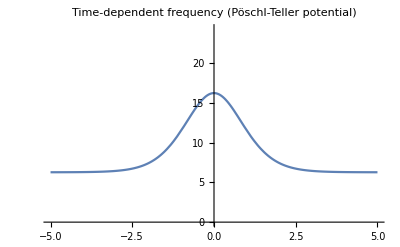

```mathematica
Plot[Evaluate[Ω[t]/.freqspec/.paramValues],relevantdomain,
PlotRange->{0,√(ω^2+α^2)*1.5/.paramValues},
PlotLabel->"Time-dependent frequency
(Pöschl-Teller potential)"]
```

### Resulting equation of motion (EOM)

#### EOM for the specified model

```mathematica
Print[Eom[t]/.freqspec," = 0"]
```

T^2 (ω^2+α^2 Sech[t/τ]^2) x[t]+x''[t] = 0

#### EOM for the specified model and parameters

```mathematica
Print[Eom[t]/.freqspec/.paramValues," = 0"]
```

T^2 (4 π^2+225 Sech[t]^2) x[t]+x''[t] = 0

## Initial time

### Small initial time (if not, the exact i.c.’s doesn’t compute)

Here we’ll choose the initial time at  − 2 · 4π / ω. This sets it at a maximum of the harmonic oscillator solution (any value − 2π k / ω is equally good for that). At that time, the oscillator will start still and from the chosen maximum amplitude value:

```mathematica
ti=−2*4π/ω/.paramValues
```

-4

Let us redefine the relevant time domain so it starts at  ti and ends at  Abs[ti]:

```mathematica
tf=Abs[ti];
relevantdomain={t,ti,tf}
```

{t,-4,4}

### Larger initial time (to see the breakdown of the approximation; skip the exact solution and only compare with numerics)

```mathematica
(*ti=-30;*)
```

## Solutions and their plots

## Exact solution

### General solution

This oscillator has exact solution in terms of hypergeometric functions:

```mathematica
soltExact=DSolve[{Eom[t]==0(*,x[ti]==A,x'[ti]==-ⅈ T Ω[ti]-Ω'[ti]/(2Ω[ti])*)}/.freqspec,x[t],t]//Flatten
```

{x[t]→(ⅇ^((2 t)/τ))^(-1/2+1/2 (1-ⅈ T τ ω)) (1+ⅇ^((2 t)/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) C[1] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^((2 t)/τ)]+(-1)^(ⅈ T τ ω) (-ⅇ^((2 t)/τ))^(ⅈ T τ ω) (ⅇ^((2 t)/τ))^(-1/2+1/2 (1-ⅈ T τ ω)) (1+ⅇ^((2 t)/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) C[2] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^((2 t)/τ)]}

```mathematica
xExact[ω_,α_,τ_,T_][t_]=x[t]/.soltExact;
```

### Integration constants

The chosen initial conditions set the values for the integration constants C[1] and C[2].

#### Analytical computation (quite slow)

```mathematica
xExact[ω,α,τ,T][ti]
```

(ⅇ^(-8/τ))^(-1/2+1/2 (1-ⅈ T τ ω)) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) C[1] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+(-1)^(ⅈ T τ ω) (-ⅇ^(-8/τ))^(ⅈ T τ ω) (ⅇ^(-8/τ))^(-1/2+1/2 (1-ⅈ T τ ω)) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) C[2] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]

```mathematica
(*AbsoluteTiming[Solve[{
xExact[ω,α,τ,T][ti]==A/√T,
xExact[ω,α,τ,T]'[ti]==-ⅈ A √T Ω[ti]-A Ω'[ti]/(2 √T Ω[ti])/.freqspec},
{C[1],C[2]}]//Flatten]
icExactParam[A_,ω_,α_,τ_,T_]=%[[2]];*)
```

↪︎ Problem: They are so big that they take forever to both be computed, and taken into account (e.g. in plots).

#### Printing of the analytical result (already computed)

{180.797,{C[1]→-((1/(√T)A (-2 ⅈ (-1)^(1+2 ⅈ T τ ω) ⅇ^(-(8 (-1+ⅈ T τ ω))/τ-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) T ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ 2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (-1/2+1/2 (1-ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ(-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(-1+1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-1/(τ (1+ⅈ T τ ω))2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω) (ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)])+(-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)] (ⅈ A √T √(ω^2+α^2 Sech[4/τ]^2)+(A α^2 Sech[4/τ]^2 Tanh[4/τ])/(2 √T τ (ω^2+α^2 Sech[4/τ]^2))))/((-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/τ 2 ⅇ^(-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (-1/2+1/2 (1-ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ ⅇ^(-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(-1+1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]-1/(2 τ (1-ⅈ T τ ω))ⅇ^(-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1+√(1+4 T^2 α^2 τ^2)) (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅇ^(-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] (-2 ⅈ (-1)^(1+2 ⅈ T τ ω) ⅇ^(-(8 (-1+ⅈ T τ ω))/τ-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) T ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ 2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (-1/2+1/2 (1-ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ(-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(-1+1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-1/(τ (1+ⅈ T τ ω))2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω) (ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]))),C[2]→((-1)^(-2 ⅈ T τ ω) ⅇ^(4/τ+4 ⅈ T ω) (1+ⅇ^(-8/τ))^(-1/2 √(1+4 T^2 α^2 τ^2)) (2 ⅈ A ⅇ^(8/τ) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(8/τ) T τ ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(16/τ) T τ ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) T^2 τ^2 ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(8/τ) T^3 τ^3 ω^5 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(16/τ) T^3 τ^3 ω^5 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-4 ⅈ A T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-4 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]+4 A T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]+4 A ⅇ^(8/τ) T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A T^2 τ^2 ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) T^2 τ^2 ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) α^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 ⅈ A ⅇ^(8/τ) α^2 √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(8/τ) T α^2 τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(16/τ) T α^2 τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(8/τ) T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(16/τ) T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A α^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) α^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-4 ⅈ A T^2 α^4 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-4 ⅈ A ⅇ^(8/τ) T^2 α^4 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A α^2 √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) α^2 √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+4 A T^3 α^4 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+4 A ⅇ^(8/τ) T^3 α^4 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A T^2 α^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 A ⅇ^(8/τ) T τ ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T τ ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(8/τ) T^3 τ^3 ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T^3 τ^3 ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(8/τ) T α^2 τ Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T α^2 τ Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(8/τ) T^3 α^2 τ^3 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T^3 α^2 τ^3 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)+ⅈ A ⅇ^(8/τ) α^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]+ⅈ A ⅇ^(16/τ) α^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]+ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]+ⅈ A ⅇ^(16/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]))/(2 √((1+ⅇ^(8/τ)) T) (2 ⅇ^(8/τ) T τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(16/τ) T τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(8/τ) T^3 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(16/τ) T^3 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ T^2 α^2 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ ⅇ^(8/τ) T^2 α^2 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 T^3 α^2 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(8/τ) T^3 α^2 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ T^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) T^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ T^2 α^2 τ^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ ⅇ^(8/τ) T^2 α^2 τ^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 T^3 α^2 τ^3 ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(8/τ) T^3 α^2 τ^3 ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ T^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) T^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]) (ω^2+α^2 Sech[4/τ]^2))}}

```mathematica
icExactParam[A_,ω_,α_,τ_,T_]={C[1]->-((1/(√T)A (-2 ⅈ (-1)^(1+2 ⅈ T τ ω) ⅇ^(-(8 (-1+ⅈ T τ ω))/τ-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) T ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ 2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (-1/2+1/2 (1-ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ(-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(-1+1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-1/(τ (1+ⅈ T τ ω))2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω) (ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)])+(-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)] (ⅈ A √T √(ω^2+α^2 Sech[4/τ]^2)+(A α^2 Sech[4/τ]^2 Tanh[4/τ])/(2 √T τ (ω^2+α^2 Sech[4/τ]^2))))/((-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/τ 2 ⅇ^(-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (-1/2+1/2 (1-ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ ⅇ^(-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(-1+1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]-1/(2 τ (1-ⅈ T τ ω))ⅇ^(-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1+√(1+4 T^2 α^2 τ^2)) (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅇ^(-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] (-2 ⅈ (-1)^(1+2 ⅈ T τ ω) ⅇ^(-(8 (-1+ⅈ T τ ω))/τ-(8 (1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) T ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ 2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (-1/2+1/2 (1-ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+1/τ(-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(-1+1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-1/(τ (1+ⅈ T τ ω))2 (-1)^(2 ⅈ T τ ω) ⅇ^(-8/τ-8 ⅈ T ω-(8 (-1/2+1/2 (1-ⅈ T τ ω)))/τ) (1+ⅇ^(-8/τ))^(1/2 (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω))) (1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω) (ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω)) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]))),C[2]->((-1)^(-2 ⅈ T τ ω) ⅇ^(4/τ+4 ⅈ T ω) (1+ⅇ^(-8/τ))^(-1/2 √(1+4 T^2 α^2 τ^2)) (2 ⅈ A ⅇ^(8/τ) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(8/τ) T τ ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(16/τ) T τ ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) T^2 τ^2 ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(8/τ) T^3 τ^3 ω^5 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 A ⅇ^(16/τ) T^3 τ^3 ω^5 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-4 ⅈ A T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-4 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]+4 A T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]+4 A ⅇ^(8/τ) T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A T^2 τ^2 ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) T^2 τ^2 ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ A ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^4 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ A ⅇ^(8/τ) α^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 ⅈ A ⅇ^(8/τ) α^2 √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(8/τ) T α^2 τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(16/τ) T α^2 τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(8/τ) T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+2 A ⅇ^(16/τ) T^3 α^2 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A α^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) α^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-4 ⅈ A T^2 α^4 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-4 ⅈ A ⅇ^(8/τ) T^2 α^4 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A α^2 √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) α^2 √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+4 A T^3 α^4 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2+4 A ⅇ^(8/τ) T^3 α^4 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A T^2 α^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2-2 A ⅇ^(8/τ) T τ ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T τ ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(8/τ) T^3 τ^3 ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T^3 τ^3 ω^4 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(8/τ) T α^2 τ Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T α^2 τ Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(8/τ) T^3 α^2 τ^3 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)-2 A ⅇ^(16/τ) T^3 α^2 τ^3 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 √(ω^2+α^2 Sech[4/τ]^2)+ⅈ A ⅇ^(8/τ) α^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]+ⅈ A ⅇ^(16/τ) α^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]+ⅈ A ⅇ^(8/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]+ⅈ A ⅇ^(16/τ) T^2 α^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Sech[4/τ]^2 Tanh[4/τ]))/(2 √((1+ⅇ^(8/τ)) T) (2 ⅇ^(8/τ) T τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(16/τ) T τ ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(8/τ) T^3 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(16/τ) T^3 τ^3 ω^3 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ T^2 α^2 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-2 ⅈ ⅇ^(8/τ) T^2 α^2 τ^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 T^3 α^2 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(8/τ) T^3 α^2 τ^3 ω Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ T^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) T^2 τ^2 ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]-ⅈ ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2)),1+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ T^2 α^2 τ^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅈ ⅇ^(8/τ) T^2 α^2 τ^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) √(1+4 T^2 α^2 τ^2) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 T^3 α^2 τ^3 ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+2 ⅇ^(8/τ) T^3 α^2 τ^3 ω Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ T^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) T^2 τ^2 ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]+ⅈ ⅇ^(8/τ) T^2 τ^2 √(1+4 T^2 α^2 τ^2) ω^2 Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1+1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,1+ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),2+ⅈ T τ ω,-ⅇ^(-8/τ)]) (ω^2+α^2 Sech[4/τ]^2))};
```

#### Numerically

We can convert all the analytical functions involved to numerical values, which speeds the handling considerably (although it’s still a bit slow; but manageable):

```mathematica
(*icExactParam[A_,ω_,α_,τ_,T_]=icExactParam[A,ω,α,τ,T]//N;*)
```

We can also compute them directly numerically:

```mathematica
icExactParam[A_,ω_,α_,τ_,T_]=NSolve[{
xExact[ω,α,τ,T][ti]==A/√T,
xExact[ω,α,τ,T]'[ti]==-ⅈ A √T Ω[ti]-A Ω'[ti]/(2 √T Ω[ti])/.freqspec},
{C[1],C[2]}]//Flatten
```

```mathematica
icExactParam[A,ω,α,τ,T]/.paramValues/.T->1//N
```

{C[1]→1.00184+0.0117187 ⅈ,C[2]→-6.43504×10^12+1.07188×10^12 ⅈ}

#### For the sample parameters

```mathematica
icExactValues=Solve[{
xExact[ω,α,τ,T][ti]==A/√T,
xExact[ω,α,τ,T]'[ti]==-ⅈ A √T Ω[ti]-A Ω'[ti]/(2 √T Ω[ti])/.freqspec}/.paramValues,
{C[1],C[2]}]//Flatten//N;
```

```mathematica
icExactValues/.T->1
```

{C[1]→1.00184+0.0117187 ⅈ,C[2]→-6.43504×10^12+1.07188×10^12 ⅈ}

### Solution with the initial conditions incorporated (very slow)

```mathematica
soltExactX=DSolve[{Eom[t]==0,x[ti]==A(*,x'[ti]==-ⅈ T Ω[ti]-Ω'[ti]/(2Ω[ti])*)}/.freqspec,x[t],t]//Flatten
```

{x[t]→((-1)^(-ⅈ T τ ω) ⅇ^(4/τ+8 ⅈ T ω) (ⅇ^((2 t)/τ))^(-1/2 ⅈ T τ ω) (1+ⅇ^(-8/τ))^(-1/2 √(1+4 T^2 α^2 τ^2)) (1+ⅇ^((2 t)/τ))^(1/2+1/2 √(1+4 T^2 α^2 τ^2)) ((-1)^(ⅈ T τ ω) ⅇ^(-4/τ-8 ⅈ T ω) (1+ⅇ^(-8/τ))^(1/2 √(1+4 T^2 α^2 τ^2)) √(1+ⅇ^(8/τ)) C[1] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^((2 t)/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)]+A ⅇ^(-4 ⅈ T ω) (-ⅇ^((2 t)/τ))^(ⅈ T τ ω) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^((2 t)/τ)]-ⅇ^(-4/τ) (-ⅇ^((2 t)/τ))^(ⅈ T τ ω) (1+ⅇ^(-8/τ))^(1/2 √(1+4 T^2 α^2 τ^2)) √(1+ⅇ^(8/τ)) C[1] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2)),1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1-ⅈ T τ ω,-ⅇ^(-8/τ)] Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^((2 t)/τ)]))/(√(1+ⅇ^(8/τ)) Hypergeometric2F1[1/2 (1+√(1+4 T^2 α^2 τ^2))+ⅈ T τ ω,ⅈ T τ ω+1/2 (1+√(1+4 T^2 α^2 τ^2)-2 ⅈ T τ ω),1+ⅈ T τ ω,-ⅇ^(-8/τ)])}

```mathematica
soltExactD=DSolve[{Eom[t]==0,(*x[ti]==A,*)x'[ti]==-ⅈ A √T Ω[ti]-A Ω'[ti]/(2 √T Ω[ti])}/.freqspec,x[t],t]//Flatten
```

```mathematica
soltExactIC=DSolve[{Eom[t]==0,x[ti]==A,x'[ti]==-ⅈ A √T Ω[ti]-A Ω'[ti]/(2 √T Ω[ti])}/.freqspec,x[t],t]//Flatten
```

### Plots

#### General (slow)

```mathematica
(*AbsoluteTiming[
Plot[Evaluate[Re[
xExact[ω,α,τ,T][t]
]]/.icExactParam[A,ω,α,τ,T]/.paramValues/.T->1,
relevantdomain,
PlotLabel->"Exact solution"]
]*)
```

Print:

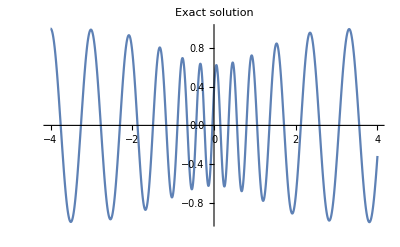
{40.742,-Graphics-}

We can speed it up lowering the number of PlotPoints:

```mathematica
(*AbsoluteTiming[
Plot[Evaluate[Re[
xExact[ω,α,τ,T][t]
]]/.icExactParam[A,ω,α,τ,T]/.paramValues/.T->1,
relevantdomain,
PlotLabel->"Exact solution",PlotPoints->10]
]*)
```

Print:

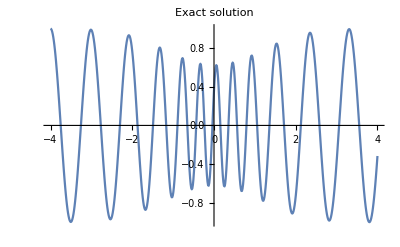
{12.5177,-Graphics-}

#### Specific values (faster)

```mathematica
(*plotExactValues=Plot[Evaluate[Re[
xExact[ω,α,τ,T][t]
]]/.icExactValues/.paramValues/.T->1,
relevantdomain,
PlotLabel->"Exact solution"]*)
```

Print:

-Graphics-

```mathematica
(*Plot[Evaluate[Re[
xExact[ω,α,τ,T][t]
]]/.icExactValues/.paramValues/.T->2,
relevantdomain,
PlotLabel->"Exact solution"]*)
```

Print:

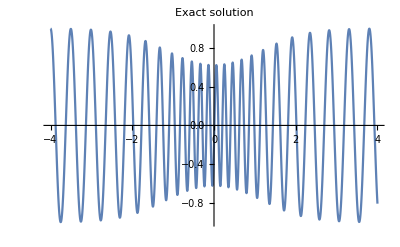

## Numerical solution

Initial conditions:		x(t_0)=A/(√T), x'(t_0)=-ⅈ T A/(√T)Ω(t_0)-A/(√T)(Ω'(t_0))/(2Ω(t_0))

### Parameters for numerics

```mathematica
tmin=-100;
tmax=100;
```

### Numerical solution

#### Computation

```mathematica
paramList
```

{A,ϕ,ω,α,τ,T}

```mathematica
Eom[t]
```

T^2 x[t] Ω[t]^2+x''[t]

```mathematica
soltNum=ParametricNDSolve[{Eom[t]==0,x[ti]==A/(√T),x'[ti]==-ⅈ T A/(√T)Ω[ti]-A/(√T)Ω'[ti]/(2Ω[ti])}/.freqspec,x[t],{t,tmin,tmax},{A,ω,α,τ,T}]//Flatten
```

{x[t]→ParametricFunction[<>]}

```mathematica
xNum[t_]=x[t]/.soltNum
```

ParametricFunction[<>]

```mathematica
paramValues
```

{A→1,ω→2 π,α→15,τ→1}

```mathematica
xNum[t][A,ω,α,τ,T]/.paramValues/.T->1
xNum[t][A,ω,α,τ,T]/.paramValues/.T->1/.t->ti
```

InterpolatingFunction[…][t]

1.+0. ⅈ

#### Static plot

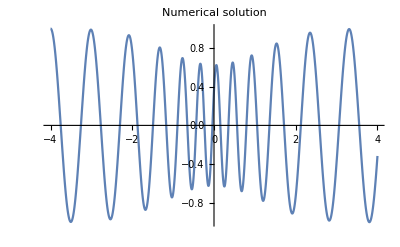

```mathematica
plotNumValues=Plot[Evaluate[Re[
xNum[t][A,ω,α,τ,T]
]]/.paramValues/.T->1,
relevantdomain,
PlotLabel->"Numerical solution"]
```

## Adiabatic solution

### Corresponding adiabatic functions and solutions

#### Adiabatic functions

Order by order:

```mathematica
For[n=0,n<=adbOrd+1,n++,{

 wCoeff[n][t_]= wCoeff[n][t]/.freqspec//FullSimplify,

Print["Order ",n,":"],
Print[wCoeff[n],"[t] = ", wCoeff[n][t]]
}];
```

Order 0:

wCoeff[0][t] = √(ω^2+α^2 Sech[t/τ]^2)

Order 1:

wCoeff[1][t] = 0

Order 2:

wCoeff[2][t] = (α^2 Sech[t/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4))/(8 τ^2 (ω^2+α^2 Sech[t/τ]^2)^(5/2))

Order 3:

wCoeff[3][t] = 0

Altogether:

```mathematica
Print["fnW[t] = ",fnW[t]]
```

fnW[t] = √(ω^2+α^2 Sech[t/τ]^2)+(α^2 Sech[t/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4) ϵ^2)/(8 τ^2 (ω^2+α^2 Sech[t/τ]^2)^(5/2))+O[ϵ]^4

#### Integrals of the adiabatic functions

↪ Takes a moment above 0^th order, but computes.

```mathematica
For[n=0,n<=adbOrd+1,n=n+2,{

intWCoeff[n][t_]= intWCoeff[n][t]/.freqspec,

Print["Order ",n,":"],
Print["∫",wCoeff[n],"[t]ⅆt = ",intWCoeff[n][t]]
}];
```

Order 0:

∫wCoeff[0][t]ⅆt = (√2 τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])

Order 2:

∫wCoeff[2][t]ⅆt = ((α^2 (2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])^(5/2) Sech[t/τ] (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4) (-((α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))+(4 ω^2 Sinh[t/τ]^3)/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))-(2 (α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2)^2 √(α^2+ω^2+ω^2 Sinh[t/τ]^2))-(α^2 Sech[t/τ]^7 Tanh[t/τ] (1575 (α^2+ω^2)^5 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6-3150 α^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^2+2100 ω^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^2+1575 α^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^4-4200 α^2 ω^2 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^4+840 ω^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^4+2100 α^4 ω^2 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^6-1680 α^2 ω^4 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^6+840 α^4 ω^4 (α^2+ω^2) ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^8+(1120 α^4 ω^4 (α^2+ω^2 Cosh[t/τ]^2) Sinh[t/τ]^8)/(√((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2)))-1575 (α^2+ω^2)^5 Cosh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2100 α^2 (α^2+ω^2)^4 Cosh[t/τ]^4 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-2100 ω^2 (α^2+ω^2)^4 Cosh[t/τ]^6 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2800 α^2 ω^2 (α^2+ω^2)^3 Cosh[t/τ]^4 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-840 ω^4 (α^2+ω^2)^3 Cosh[t/τ]^6 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+96 α^6 (α^2+ω^2)^2 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 (α^2+ω^2)^2 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+168 α^6 ω^2 (α^2+ω^2) Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+48 α^6 ω^2 (α^2+ω^2) HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+72 α^6 ω^4 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 ω^4 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))))/(315 (α^2+ω^2)^7 √(((α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2)/(α^2+ω^2)) √(α^2+ω^2+ω^2 Sinh[t/τ]^2) (1+(ω^2 Sinh[t/τ]^2)/(α^2+ω^2)) ((α^2 Tanh[t/τ]^2)/(α^2+ω^2))^(5/2))))/(16 √2 τ (-3 α^2-3 ω^2-α^2 Cosh[(2 t)/τ]-2 ω^2 Cosh[(2 t)/τ]+ω^2 Cosh[(4 t)/τ]) (ω^2+α^2 Sech[t/τ]^2)^(5/2)))

#### Full adiabatic solution

```mathematica
xAdb[A,ϕ,T][t]
```

(A ⅇ^(-ⅈ T ϕ-ⅈ T ((√2 τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+(α^2 ϵ^2 (2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])^(5/2) Sech[t/τ] (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4) (-((α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))+(4 ω^2 Sinh[t/τ]^3)/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))-(2 (α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2)^2 √(α^2+ω^2+ω^2 Sinh[t/τ]^2))-(α^2 Sech[t/τ]^7 Tanh[t/τ] (1575 (α^2+ω^2)^5 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6-3150 α^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^2+2100 ω^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^2+1575 α^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^4-4200 α^2 ω^2 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^4+840 ω^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^4+2100 α^4 ω^2 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^6-1680 α^2 ω^4 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^6+840 α^4 ω^4 (α^2+ω^2) ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^8+(1120 α^4 ω^4 (α^2+ω^2 Cosh[t/τ]^2) Sinh[t/τ]^8)/(√((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2)))-1575 (α^2+ω^2)^5 Cosh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2100 α^2 (α^2+ω^2)^4 Cosh[t/τ]^4 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-2100 ω^2 (α^2+ω^2)^4 Cosh[t/τ]^6 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2800 α^2 ω^2 (α^2+ω^2)^3 Cosh[t/τ]^4 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-840 ω^4 (α^2+ω^2)^3 Cosh[t/τ]^6 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+96 α^6 (α^2+ω^2)^2 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 (α^2+ω^2)^2 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+168 α^6 ω^2 (α^2+ω^2) Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+48 α^6 ω^2 (α^2+ω^2) HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+72 α^6 ω^4 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 ω^4 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))))/(315 (α^2+ω^2)^7 √(((α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2)/(α^2+ω^2)) √(α^2+ω^2+ω^2 Sinh[t/τ]^2) (1+(ω^2 Sinh[t/τ]^2)/(α^2+ω^2)) ((α^2 Tanh[t/τ]^2)/(α^2+ω^2))^(5/2))))/(16 √2 τ (-3 α^2-3 ω^2-α^2 Cosh[(2 t)/τ]-2 ω^2 Cosh[(2 t)/τ]+ω^2 Cosh[(4 t)/τ]) (ω^2+α^2 Sech[t/τ]^2)^(5/2)))) √(√(ω^2+α^2 Sech[4/τ]^2)+(α^2 ϵ^2 Sech[4/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[4/τ]^2+α^2 Sech[4/τ]^4))/(8 τ^2 (ω^2+α^2 Sech[4/τ]^2)^(5/2))))/(√(T (√(ω^2+α^2 Sech[t/τ]^2)+(α^2 ϵ^2 Sech[t/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4))/(8 τ^2 (ω^2+α^2 Sech[t/τ]^2)^(5/2)))))

#### Solution’s terms order by order

```mathematica
For[n=0,n<=adbOrd,n++,{
Print["Order ",n,":"],
Print[xAdbTaylorCoeff[n],"[t] = ", xAdbTaylorCoeff[n][t]]
}];
```

Order 0:

xAdbTaylorCoeff[0][t] = 1/(T √(ω^2+α^2 Sech[t/τ]^2))A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) (ω^2+α^2 Sech[4/τ]^2)^(1/4) √(T √(ω^2+α^2 Sech[t/τ]^2))

Order 1:

xAdbTaylorCoeff[1][t] = 0

Order 2:

xAdbTaylorCoeff[2][t] = (A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) α^2 Sech[4/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[4/τ]^2+α^2 Sech[4/τ]^4) √(T √(ω^2+α^2 Sech[t/τ]^2)))/(16 T τ^2 (ω^2+α^2 Sech[4/τ]^2)^(11/4) √(ω^2+α^2 Sech[t/τ]^2))-1/(16 T τ^2 (ω^2+α^2 Sech[t/τ]^2)^(7/2))A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) α^2 (ω^2+α^2 Sech[4/τ]^2)^(1/4) Sech[t/τ]^2 √(T √(ω^2+α^2 Sech[t/τ]^2)) (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4)-(ⅈ A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) α^2 (2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])^(5/2) (ω^2+α^2 Sech[4/τ]^2)^(1/4) Sech[t/τ] √(T √(ω^2+α^2 Sech[t/τ]^2)) (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4) (-((α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))+(4 ω^2 Sinh[t/τ]^3)/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))-(2 (α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2)^2 √(α^2+ω^2+ω^2 Sinh[t/τ]^2))-(α^2 Sech[t/τ]^7 Tanh[t/τ] (1575 (α^2+ω^2)^5 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6-3150 α^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^2+2100 ω^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^2+1575 α^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^4-4200 α^2 ω^2 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^4+840 ω^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^4+2100 α^4 ω^2 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^6-1680 α^2 ω^4 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^6+840 α^4 ω^4 (α^2+ω^2) ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^8+(1120 α^4 ω^4 (α^2+ω^2 Cosh[t/τ]^2) Sinh[t/τ]^8)/(√((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2)))-1575 (α^2+ω^2)^5 Cosh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2100 α^2 (α^2+ω^2)^4 Cosh[t/τ]^4 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-2100 ω^2 (α^2+ω^2)^4 Cosh[t/τ]^6 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2800 α^2 ω^2 (α^2+ω^2)^3 Cosh[t/τ]^4 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-840 ω^4 (α^2+ω^2)^3 Cosh[t/τ]^6 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+96 α^6 (α^2+ω^2)^2 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 (α^2+ω^2)^2 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+168 α^6 ω^2 (α^2+ω^2) Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+48 α^6 ω^2 (α^2+ω^2) HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+72 α^6 ω^4 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 ω^4 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))))/(315 (α^2+ω^2)^7 √(((α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2)/(α^2+ω^2)) √(α^2+ω^2+ω^2 Sinh[t/τ]^2) (1+(ω^2 Sinh[t/τ]^2)/(α^2+ω^2)) ((α^2 Tanh[t/τ]^2)/(α^2+ω^2))^(5/2))))/(16 √2 τ (-3 α^2-3 ω^2-α^2 Cosh[(2 t)/τ]-2 ω^2 Cosh[(2 t)/τ]+ω^2 Cosh[(4 t)/τ]) (ω^2+α^2 Sech[t/τ]^2)^3)

```mathematica
Print["xAdbTaylor[A,ϕ,T][t] = ",xAdbTaylor[A,ϕ,T][t]]
```

xAdbTaylor[A,ϕ,T][t] = 1/(T √(ω^2+α^2 Sech[t/τ]^2))A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) (ω^2+α^2 Sech[4/τ]^2)^(1/4) √(T √(ω^2+α^2 Sech[t/τ]^2))+((A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) α^2 Sech[4/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[4/τ]^2+α^2 Sech[4/τ]^4) √(T √(ω^2+α^2 Sech[t/τ]^2)))/(16 T τ^2 (ω^2+α^2 Sech[4/τ]^2)^(11/4) √(ω^2+α^2 Sech[t/τ]^2))-1/(16 T τ^2 (ω^2+α^2 Sech[t/τ]^2)^(7/2))A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) α^2 (ω^2+α^2 Sech[4/τ]^2)^(1/4) Sech[t/τ]^2 √(T √(ω^2+α^2 Sech[t/τ]^2)) (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4)-(ⅈ A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) α^2 (2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])^(5/2) (ω^2+α^2 Sech[4/τ]^2)^(1/4) Sech[t/τ] √(T √(ω^2+α^2 Sech[t/τ]^2)) (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4) (-((α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))+(4 ω^2 Sinh[t/τ]^3)/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))-(2 (α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2)^2 √(α^2+ω^2+ω^2 Sinh[t/τ]^2))-(α^2 Sech[t/τ]^7 Tanh[t/τ] (1575 (α^2+ω^2)^5 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6-3150 α^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^2+2100 ω^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^2+1575 α^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^4-4200 α^2 ω^2 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^4+840 ω^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^4+2100 α^4 ω^2 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^6-1680 α^2 ω^4 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^6+840 α^4 ω^4 (α^2+ω^2) ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^8+(1120 α^4 ω^4 (α^2+ω^2 Cosh[t/τ]^2) Sinh[t/τ]^8)/(√((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2)))-1575 (α^2+ω^2)^5 Cosh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2100 α^2 (α^2+ω^2)^4 Cosh[t/τ]^4 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-2100 ω^2 (α^2+ω^2)^4 Cosh[t/τ]^6 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2800 α^2 ω^2 (α^2+ω^2)^3 Cosh[t/τ]^4 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-840 ω^4 (α^2+ω^2)^3 Cosh[t/τ]^6 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+96 α^6 (α^2+ω^2)^2 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 (α^2+ω^2)^2 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+168 α^6 ω^2 (α^2+ω^2) Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+48 α^6 ω^2 (α^2+ω^2) HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+72 α^6 ω^4 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 ω^4 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))))/(315 (α^2+ω^2)^7 √(((α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2)/(α^2+ω^2)) √(α^2+ω^2+ω^2 Sinh[t/τ]^2) (1+(ω^2 Sinh[t/τ]^2)/(α^2+ω^2)) ((α^2 Tanh[t/τ]^2)/(α^2+ω^2))^(5/2))))/(16 √2 τ (-3 α^2-3 ω^2-α^2 Cosh[(2 t)/τ]-2 ω^2 Cosh[(2 t)/τ]+ω^2 Cosh[(4 t)/τ]) (ω^2+α^2 Sech[t/τ]^2)^3)) ϵ^2+O[ϵ]^4

#### Solution’s terms up to each order

```mathematica
For[n=0,n<=adbOrd+1,n=n+2,{
Print["Up to order ",n+1,":"],
Print[ xAdbUpto[n],"[t] = ", xAdbUpto[n][t]]
}]
```

Up to order 1:

xAdbUpto[0][t] = (A ⅇ^(-ⅈ T ϕ-(ⅈ √2 T τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])) (ω^2+α^2 Sech[4/τ]^2)^(1/4))/(√(T √(ω^2+α^2 Sech[t/τ]^2)))

Up to order 3:

xAdbUpto[2][t] = ((A ⅇ^(-ⅈ T ϕ-ⅈ T ((√2 τ Cosh[t/τ] (√(α^2) ArcTan[(√2 √(α^2) Sinh[t/τ])/(√(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ]))] √(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+√(ω^2) √(α^2+ω^2) ArcSinh[(√(ω^2) Sinh[t/τ])/(√(α^2+ω^2))] √((2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])/(α^2+ω^2))) √(ω^2+α^2 Sech[t/τ]^2))/(2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])+(α^2 ϵ^2 (2 α^2+ω^2+ω^2 Cosh[(2 t)/τ])^(5/2) Sech[t/τ] (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4) (-((α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))+(4 ω^2 Sinh[t/τ]^3)/(3 (α^2+ω^2) (α^2+ω^2+ω^2 Sinh[t/τ]^2)^(3/2))-(2 (α^2+2 ω^2) Sinh[t/τ])/(3 (α^2+ω^2)^2 √(α^2+ω^2+ω^2 Sinh[t/τ]^2))-(α^2 Sech[t/τ]^7 Tanh[t/τ] (1575 (α^2+ω^2)^5 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6-3150 α^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^2+2100 ω^2 (α^2+ω^2)^4 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^2+1575 α^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^4-4200 α^2 ω^2 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^4+840 ω^4 (α^2+ω^2)^3 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^6 Sinh[t/τ]^4+2100 α^4 ω^2 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^6-1680 α^2 ω^4 (α^2+ω^2)^2 ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^4 Sinh[t/τ]^6+840 α^4 ω^4 (α^2+ω^2) ArcSin[√((α^2 Tanh[t/τ]^2)/(α^2+ω^2))] Cosh[t/τ]^2 Sinh[t/τ]^8+(1120 α^4 ω^4 (α^2+ω^2 Cosh[t/τ]^2) Sinh[t/τ]^8)/(√((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2)))-1575 (α^2+ω^2)^5 Cosh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2100 α^2 (α^2+ω^2)^4 Cosh[t/τ]^4 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-2100 ω^2 (α^2+ω^2)^4 Cosh[t/τ]^6 Sinh[t/τ]^2 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+2800 α^2 ω^2 (α^2+ω^2)^3 Cosh[t/τ]^4 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))-840 ω^4 (α^2+ω^2)^3 Cosh[t/τ]^6 Sinh[t/τ]^4 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+96 α^6 (α^2+ω^2)^2 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 (α^2+ω^2)^2 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^6 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+168 α^6 ω^2 (α^2+ω^2) Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+48 α^6 ω^2 (α^2+ω^2) HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^8 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+72 α^6 ω^4 Hypergeometric2F1[2,2,9/2,(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))+24 α^6 ω^4 HypergeometricPFQ[{2,2,2},{1,9/2},(α^2 Tanh[t/τ]^2)/(α^2+ω^2)] Sinh[t/τ]^10 √((α^2 (α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2 Tanh[t/τ]^2)/((α^2+ω^2)^2))))/(315 (α^2+ω^2)^7 √(((α^2+ω^2 Cosh[t/τ]^2) Sech[t/τ]^2)/(α^2+ω^2)) √(α^2+ω^2+ω^2 Sinh[t/τ]^2) (1+(ω^2 Sinh[t/τ]^2)/(α^2+ω^2)) ((α^2 Tanh[t/τ]^2)/(α^2+ω^2))^(5/2))))/(16 √2 τ (-3 α^2-3 ω^2-α^2 Cosh[(2 t)/τ]-2 ω^2 Cosh[(2 t)/τ]+ω^2 Cosh[(4 t)/τ]) (ω^2+α^2 Sech[t/τ]^2)^(5/2)))) √(√(ω^2+α^2 Sech[4/τ]^2)+(α^2 ϵ^2 Sech[4/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[4/τ]^2+α^2 Sech[4/τ]^4))/(8 τ^2 (ω^2+α^2 Sech[4/τ]^2)^(5/2))))/(√(T (√(ω^2+α^2 Sech[t/τ]^2)+(α^2 ϵ^2 Sech[t/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4))/(8 τ^2 (ω^2+α^2 Sech[t/τ]^2)^(5/2))))))

### Parametric versions of the adiabatic solution

```mathematica
paramList
```

{A,ϕ,ω,α,τ,T}

#### Order by order coefficients

```mathematica
For[n=0,n<=adbOrd,n++,{
 xAdbTaylorCoeff[n][A_,ϕ_,ω_,α_,τ_,T_][t_]=xAdbTaylorCoeff[n][t]
}]
```

#### Solution up to each order

```mathematica
For[n=0,n<=adbOrd+1,n=n+2,{
xAdbUpto[n][A_,ϕ_,ω_,α_,τ_,T_][t_]=xAdbUpto[n][t]/.ϵ->(1/T)
}]
```

#### Taylor-expanded solution

```mathematica
xAdbTaylor[A_,ϕ_,ω_,α_,τ_,T_][t_]= xAdbTaylor[A,ϕ,T][t];
```

#### Full adiabatic solution

```mathematica
xAdb[A_,ϕ_,ω_,α_,τ_,T_][t_]= xAdb[A,ϕ,T][t]/.ϵ->(1/T);
```

### Phase difference to match the normalized initial conditions

#### Value at zeroth order

Besides a normalized amplitude A, we seek a value for ϕ such that it sets a vanishing initial phase on the adiabatic ansatz. For this, we have to balance the quantity ∫W(t')ⅆt' at initial time, which in the code is given (to first order) by intWCoeff[0][ti]. Hence:

```mathematica
icAdbNorm[0][ω_,α_,τ_,T_]={A->1,ϕ->-intWCoeff[0][ti]//Refine//Simplify}
```

{A→1,ϕ→τ (ω ArcSinh[(ω Sinh[4/τ])/(√(α^2+ω^2))]+α ArcTan[(√2 α Sinh[4/τ])/(√(2 α^2+ω^2+ω^2 Cosh[8/τ]))])}

For the chosen values this gives:

```mathematica
icAdbNorm[0][ω,α,τ,T]/.paramValues//N
```

{1.→1.,ϕ→36.7572}

#### Meaning

The chosen initial {A,ϕ} makes the exponent of the adiabatic ansatz zero at initial time:

```mathematica
(*-*)ⅈ T(intWCoeff[0][ti]+ϕ)/.icAdbNorm[0][ω,α,τ,T]//Simplify
```

0

Hence, it is only a phase and its exponential gives one:

```mathematica
ⅇ^((*-*)ⅈ T(intWCoeff[0][ti]+ϕ))/.icAdbNorm[0][ω,α,τ,T]//Simplify
```

1

Finally, the adiabatic ansatz (to first order) at initial time is:

```mathematica
xAdbUpto[0][t]/.icAdbNorm[0][ω,α,τ,T]/.T->1/.t->ti//Refine//Simplify
N[%/.paramValues,2]
```

1

1.

#### Obs. 1: Make it lie in the angle’s [0, 2π ) range

We shall note that the above happens as well for the chosen ϕ ± any integer factor of 2π. Hence, we could also define the phase difference to subtract by the quantity:

```mathematica
icAdbNorm[0][ω_,α_,τ_,T_]={A->1,ϕ->-(intWCoeff[0][ti]-(2π)/T IntegerPart[(T intWCoeff[0][ti])/(2π)]//Refine//Simplify)};
```

```mathematica
intWCoeff[0][ti]-(2π)/T IntegerPart[(T intWCoeff[0][ti])/(2π)]//Refine//Simplify
```

-τ (ω ArcSinh[(ω Sinh[4/τ])/(√(α^2+ω^2))]+α ArcTan[(√2 α Sinh[4/τ])/(√(2 α^2+ω^2+ω^2 Cosh[8/τ]))])+(2 π IntegerPart[(T τ (ω ArcSinh[(ω Sinh[4/τ])/(√(α^2+ω^2))]+α ArcTan[(√2 α Sinh[4/τ])/(√(2 α^2+ω^2+ω^2 Cosh[8/τ]))]))/(2 π)])/T

This is taking the value of intWCoeff[0][ti] and subtracting the integer number of 2π  contained in that same intWCoeff[0][ti] (after making it an angle again, multiplying by 2π). The result makes ϕ to lie in the standard angle range [0, 2π ).

E.g. for our chosen parameters this gives:

```mathematica
-(intWCoeff[0][ti]-(2π)/T IntegerPart[(T intWCoeff[0][ti])/(2π)]//Refine//Simplify)/.paramValues/.T->1//N
```

5.34131

Let’s rather use this definition:

```mathematica
icAdbNorm[0][ω_,α_,τ_,T_]={A->1,ϕ->-(intWCoeff[0][ti]-(2π)/T IntegerPart[(T intWCoeff[0][ti])/(2π)]//Refine//Simplify)};
icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1//N
```

{1.→1.,ϕ→5.34131}

#### Obs. 2: Higher orders

We could make it more accurate by going to higher order intWCoeff[n][ti], or directly to the full intW[ti]. However, since the goal is to set initial conditions, where the zeroth order adiabatic solution is expected to still match the exact solution very well, we keep the simplest, zeroth order expression.

The above was proven wrong, so let’s go for higher orders. With the full adiabatic function it is...

```mathematica
icAdbNorm[0][ω_,α_,τ_,T_]={A->1,ϕ->-Normal[intW[t]]/.ϵ->1/.t->ti//Refine//N};
```

(The //N  is added so computations are faster, although looses some [negligible] analytic accuracy.)

```mathematica
icAdbNorm[0][ω,α,τ,T]/.paramValues//N
```

{1.→1.,ϕ→36.7531}

### Higher-order corrections

All-order adiabatic corrections in the full adiabatic solution:

```mathematica
hoAdbCorr=Normal[xAdb[A,ϕ,ω,α,τ,T][t]-xAdbTaylorCoeff[0][t]];
```

All-order adiabatic corrections in the expanded adiabatic solution:

```mathematica
hoAdbTaylorCorr=Normal[ xAdbTaylor[A,ϕ,ω,α,τ,T][t]]-xAdbTaylorCoeff[0][t];
```

### Plots

Functions to plot:

```mathematica
xAdb[A,ϕ,ω,α,τ,T][t];
Normal[xAdbTaylor[A,ϕ,ω,α,τ,T][t]];
```

#### Full adiabatic solution - Static plot

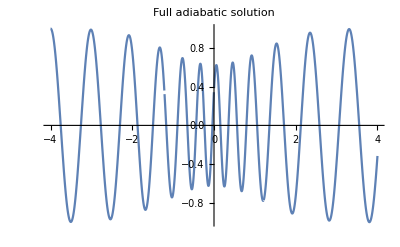

```mathematica
plotAdbFullValues=Plot[Evaluate[Re[
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1
]],relevantdomain,
PlotLabel->"Full adiabatic solution"]
```

#### Expanded adiabatic solution - Static plot

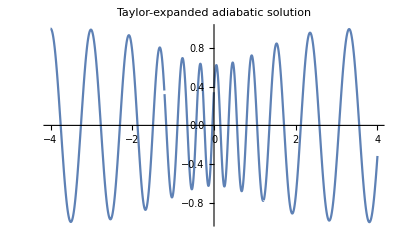

```mathematica
plotAdbTaylorValues=Plot[Evaluate[Re[
Normal[ xAdbTaylor[A,ϕ,ω,α,τ,T][t]]/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.ϵ->(1/T)/.T->1
]],relevantdomain,
PlotLabel->"Taylor-expanded adiabatic solution"]
```

#### Higher-order corrections - Static plot

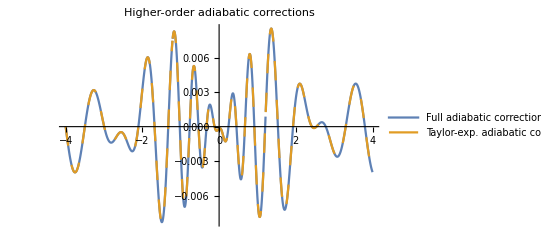

```mathematica
plotHOAdbCorrValues=Plot[Evaluate[Re[{
hoAdbCorr,
hoAdbTaylorCorr/.ϵ->(1/T)
}/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1
]],relevantdomain,
PlotStyle->stylecompare,
PlotLegends->{
"Full adiabatic corrections",
"Taylor-exp. adiabatic corrections"},
PlotLabel->"Higher-order adiabatic corrections",
PlotRange->All]
```

To make sense of the order of the corrections, here we plot it alongside the whole adiabatic solution.

Whole adiabatic solution plus all-order corrections:

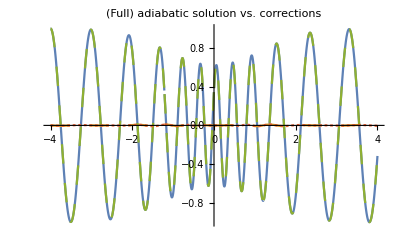

```mathematica
plotAdbSolvsCorrValues=Plot[Evaluate[Re[{
xAdb[A,ϕ,ω,α,τ,T][t],
hoAdbCorr,
Normal[xAdbTaylor[A,ϕ,ω,α,τ,T][t]]/.ϵ->(1/T),
hoAdbTaylorCorr/.ϵ->(1/T)
}/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1
]],relevantdomain,
PlotRange->All,
PlotStyle->stylecompare,
PlotLabel->"(Full) adiabatic solution vs. corrections"]
```

## Adiabatic semi-analytical solution

### Computation

#### Semi-analytics’ recall

```mathematica
Definition[ParametricNPrimitive]
```

ParametricNPrimitive[{integrand_,vari_},primitiveName_,{var_,varMin_,varMax_},paramList_]:=ParametricNDSolve[{primitiveName'[var]==integrand,primitiveName[vari]==0},primitiveName,{var,varMin,varMax},Flatten[{paramList}]]

#### Adiabatic functions W(t) to integrate (just printing)

```mathematica
wCoeff[0][t]
wCoeff[1][t]
wCoeff[2][t]
wCoeff[3][t]
```

√(ω^2+α^2 Sech[t/τ]^2)

0

(α^2 Sech[t/τ]^2 (-4 ω^2+(α^2+6 ω^2) Sech[t/τ]^2+α^2 Sech[t/τ]^4))/(8 τ^2 (ω^2+α^2 Sech[t/τ]^2)^(5/2))

0

#### Semi-analytical integrations

```mathematica
ClearAll[intWNum,soltIntWCoeffNum,intWCoeffNum,intWNumUpto]
```

```mathematica
For[n=0,n<=adbOrd+1,n++,{
soltIntWCoeffNum[n]=ParametricNPrimitive[{wCoeff[n][t],ti},intWCoeffNum[n],{t,tmin,tmax},{A,ω,α,τ}],
intWCoeffNum[n][A_,ω_,α_,τ_][s_]=intWCoeffNum[n][A,ω,α,τ][t]/.soltIntWCoeffNum[n]/.t->s
}]
```

```mathematica
intWNum[A_,ω_,α_,τ_][t_]=∑_(n=0)^adbOrd intWCoeffNum[n][A,ω,α,τ][t]
```

ParametricFunction[<>][A,ω,α,τ][t]+ParametricFunction[<>][A,ω,α,τ][t]+ParametricFunction[<>][A,ω,α,τ][t]

```mathematica
For[n=0,n<=adbOrd+1,n++,{
intWNumUpto[n][A_,ω_,α_,τ_][t_]=∑_(m=0)^n intWCoeffNum[m][A,ω,α,τ][t]
}]
```

#### Semi-analytical adiabatic solution

```mathematica
xAdbNum[A_,ω_,α_,τ_,T_][s_]=(A √(2Normal[fnW[ti]]))/(√(2T Normal[fnW[t]]))ⅇ^((**)-ⅈ T intWNum[A,ω,α,τ][t])/.ϵ->(1/T)/.t->s;
```

```mathematica
For[n=0,n<=adbOrd,n++,{
xAdbNumUpto[n][A_,ω_,α_,τ_,T_][t_]=(A √(2Normal[fnWupto[n][ti]]))/(√(2T Normal[fnWupto[n][t]]))ⅇ^((**)-ⅈ T intWNumUpto[n][A,ω,α,τ][t])/.ϵ->(1/T)
}]
```

### Plots for the full solution

#### Static plot

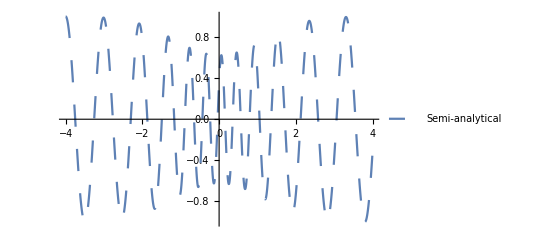

```mathematica
Plot[Evaluate[Re[{
xAdbNum[A,ω,α,τ,T][t]/.paramValues/.T->1
}]],relevantdomain,
PlotLegends->{"Semi-analytical"},
PlotStyle->Dashing[0.04]]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[Evaluate[Re[{
xAdbNum[A,ω,α,τ,T][t]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"Semi-analytical"},
PlotStyle->Dashing[0.04]
],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### Plots for the 0th-order solution

#### Static plot

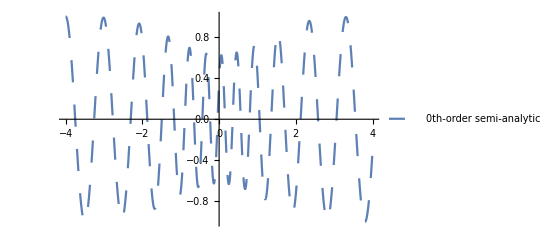

```mathematica
Plot[Evaluate[Re[{
xAdbNumUpto[0][A,ω,α,τ,T][t]/.paramValues/.T->1
}]],relevantdomain,
PlotLegends->{"0th-order semi-analytical"},
PlotStyle->Dashing[0.04]
]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[Evaluate[Re[{
xAdbNumUpto[0][A,ω,α,τ,T][t]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"0th-order semi-analytical"}
(*,PlotStyle->Dashing[0.04]*)
],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### Plots for the 2nd-order solution

#### Static plot

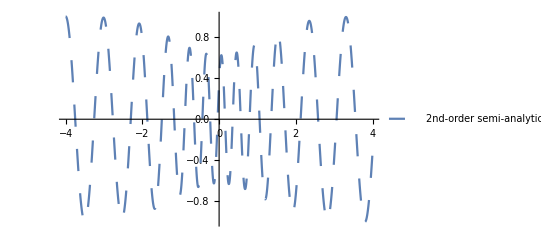

```mathematica
Plot[Evaluate[Re[{
xAdbNumUpto[2][A,ω,α,τ,T][t]/.paramValues/.T->1
}]],relevantdomain,
PlotLegends->{"2nd-order semi-analytical"},
PlotStyle->Dashing[0.04]
]
```

#### Manipulable plot

```mathematica
Manipulate[Plot[Evaluate[Re[{
xAdbNumUpto[2][A,ω,α,τ,T][t]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"2nd-order semi-analytical"},
PlotStyle->Dashing[0.04]
],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

## Detailed comparison of solutions

## Static comparisons

### Numerical vs. exact

#### Relevant domain

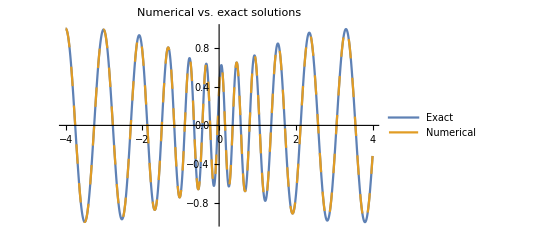

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]/.icExactValues,
xNum[t][A,ω,α,τ,T]
}/.paramValues/.T->1
]],relevantdomain,
PlotStyle->stylecompare,
PlotLegends->{"Exact","Numerical"},
PlotLabel->"Numerical vs. exact solutions"]
```

#### Larger domain

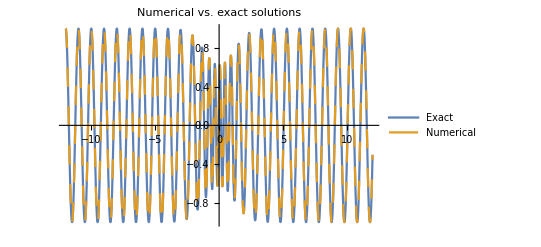

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]/.icExactValues,
xNum[t][A,ω,α,τ,T]
}/.paramValues/.T->1
]],{t,-12,12},
PlotStyle->stylecompare,
PlotLegends->{"Exact","Numerical"},
PlotLabel->"Numerical vs. exact solutions"]
```

(Obs: Here the numerical solution is actually better, since some functions inside the exact one get values beyond Mathematica’s default precision; of course that precision could be enlarged, e.g. through PlotPoints->300.)

#### Difference (~10^-6)

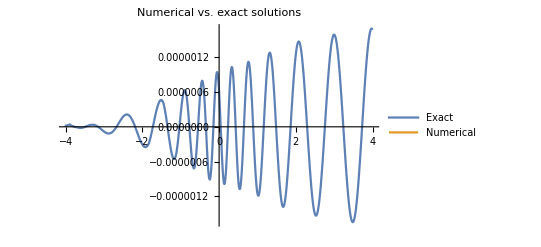

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]-xNum[t][A,ω,α,τ,T]/.icExactValues,
}/.paramValues/.T->1
]],relevantdomain,
PlotStyle->stylecompare,
PlotLegends->{"Exact","Numerical"},
PlotLabel->"Numerical vs. exact solutions"]
```

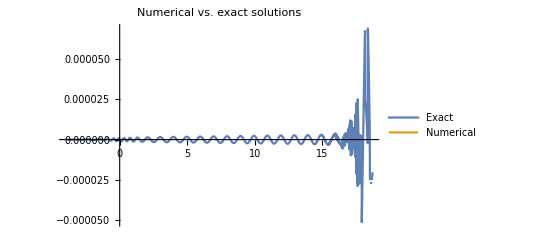

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]-xNum[t][A,ω,α,τ,T]/.icExactValues,
}/.paramValues/.T->1
]],{t,-4,20},
PlotRange->All,
PlotStyle->stylecompare,
PlotLegends->{"Exact","Numerical"},
PlotLabel->"Numerical vs. exact solutions"]
```

### Adiabatic vs. exact

#### Full adiabatic

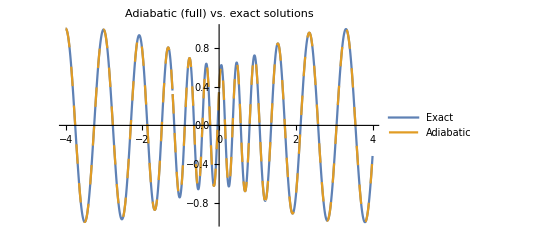

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]/.icExactValues,
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}/.paramValues/.T->1
]],relevantdomain,
PlotStyle->stylecompare,
PlotLegends->{"Exact","Adiabatic"},
PlotLabel->"Adiabatic (full) vs. exact solutions"]
```

#### Full adiabatic error

Real part of the difference:

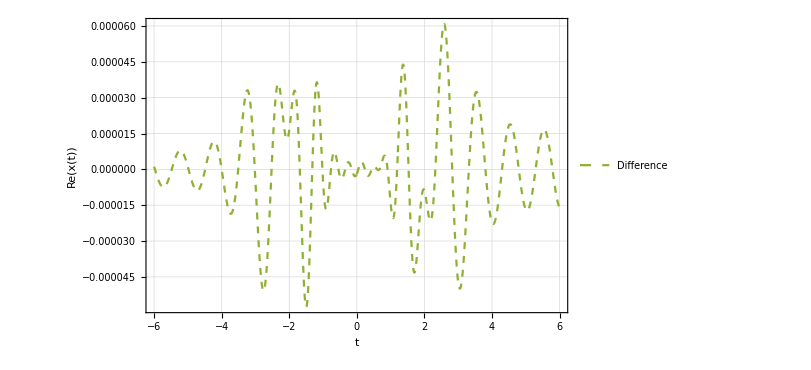

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]-xAdb[A,ϕ,ω,α,τ,T][t]
}/.icExactValues/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1
]],{t,-6,6},
PlotStyle->{ColorData[97,3],Dashed},ImageSize->600,PlotPoints->300,
BaseStyle->{FontFamily->"CMU Serif",FontSize->10},
AxesLabel->{ToExpression["t",TeXForm,HoldForm],ToExpression["\\mathrm{Re}\\left[x(t)\\right]",TeXForm,HoldForm]},
PlotLegends->Placed[LineLegend[{"Difference"},LegendFunction->(Framed[#,FrameMargins->0,FrameStyle->Gray,Background->White]&)],{Right,Bottom}],
GridLines->Automatic,Frame->True
]
```

Real part of the absolute difference:

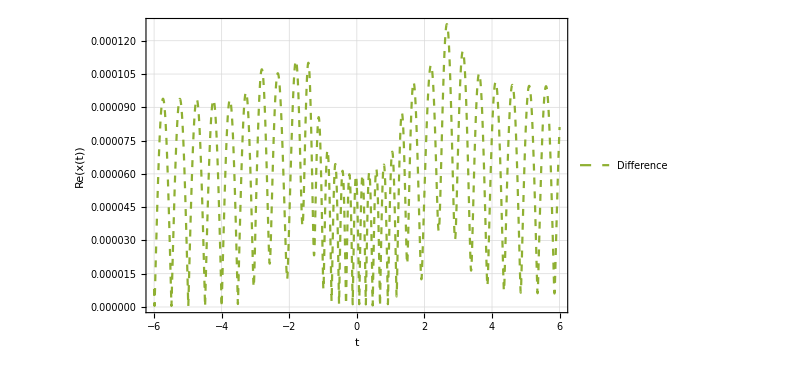

```mathematica
Plot[Evaluate[Re@Abs[{
xExact[ω,α,τ,T][t]-xAdb[A,ϕ,ω,α,τ,T][t]
}/.icExactValues/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1
]],{t,-6,6},
PlotStyle->{ColorData[97,3],Dashed},ImageSize->600,PlotPoints->300,
BaseStyle->{FontFamily->"CMU Serif",FontSize->10},
AxesLabel->{ToExpression["t",TeXForm,HoldForm],ToExpression["\\mathrm{Re}\\left[x(t)\\right]",TeXForm,HoldForm]},
PlotLegends->Placed[LineLegend[{"Difference"},LegendFunction->(Framed[#,FrameMargins->0,FrameStyle->Gray,Background->White]&)],{Right,Bottom}],
GridLines->Automatic,Frame->True
]
```

#### Expanded adiabatic

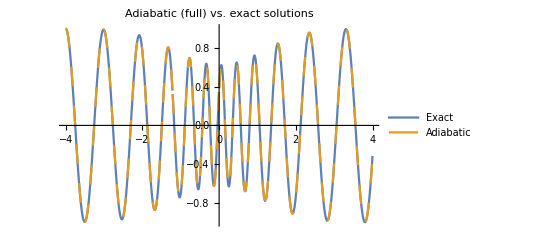

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]/.icExactValues,
Normal[xAdbTaylor[A,ϕ,ω,α,τ,T][t]]/.icAdbNorm[0][ω,α,τ,T]/.ϵ->(1/T)
}/.paramValues/.T->1
]],relevantdomain,
PlotStyle->stylecompare,
PlotLegends->{"Exact","Adiabatic"},
PlotLabel->"Adiabatic (full) vs. exact solutions"]
```

#### Adiabatic solutions up to each order

Full adiabatic solutions up to each order:

```mathematica
(*{xAdbTaylorCoeff[0][t],
Array[xAdbTaylorCoeff[#][t]&,adbOrd]}//Flatten;*)
```

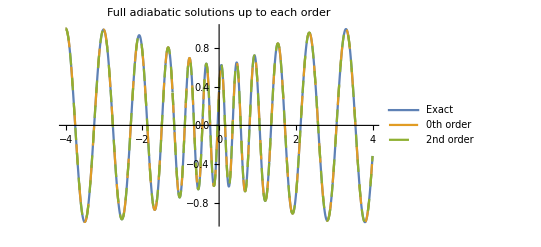

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]/.icExactValues,
xAdbUpto[0][A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T],
xAdbUpto[2][A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}/.paramValues/.T->1
]],relevantdomain,
PlotStyle->styleall,
PlotPoints->300,
PlotLegends->legendorders,
PlotLabel->"Full adiabatic solutions up to each order"]
```

For better or worse, higher orders barely improve the approximation, or don’t even do it at all.

Expanded adiabatic solutions up to each order:

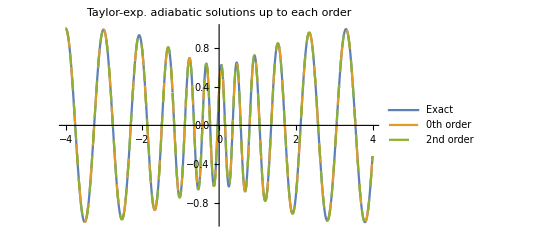

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]/.icExactValues,
Normal[xAdbTaylor[A,ϕ,ω,α,τ,T][t]+O[ϵ]^1]/.icAdbNorm[0][ω,α,τ,T]/.ϵ->(1/T),
Normal[xAdbTaylor[A,ϕ,ω,α,τ,T][t]+O[ϵ]^3]/.icAdbNorm[0][ω,α,τ,T]/.ϵ->(1/T)
}/.paramValues/.T->1
]],relevantdomain,
PlotStyle->styleall,
PlotPoints->300,
PlotLegends->legendorders,
PlotLabel->"Taylor-exp. adiabatic solutions up to each order"]
```

#### 0th-order error

Real part of the difference:

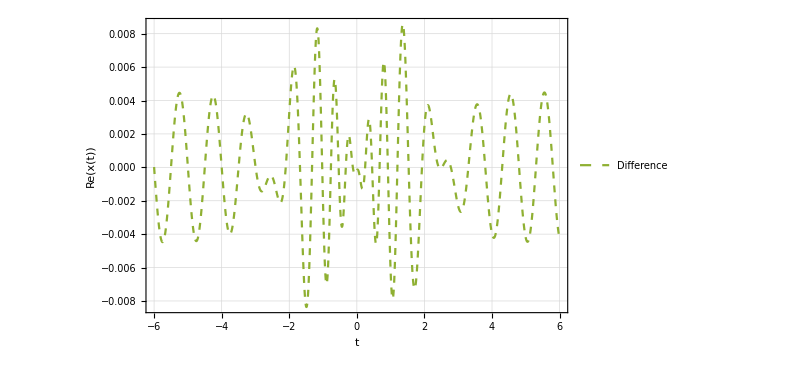

```mathematica
Plot[Evaluate[Re[{
xExact[ω,α,τ,T][t]-xAdbUpto[0][A,ϕ,ω,α,τ,T][t]
}/.icExactValues/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1
]],{t,-6,6},
PlotStyle->{ColorData[97,3],Dashed},ImageSize->600,PlotPoints->300,
BaseStyle->{FontFamily->"CMU Serif",FontSize->10},
AxesLabel->{ToExpression["t",TeXForm,HoldForm],ToExpression["\\mathrm{Re}\\left[x(t)\\right]",TeXForm,HoldForm]},
PlotLegends->Placed[LineLegend[{"Difference"},LegendFunction->(Framed[#,FrameMargins->0,FrameStyle->Gray,Background->White]&)],{Right,Bottom}],
GridLines->Automatic,Frame->True
]
```

Real part of the absolute difference:

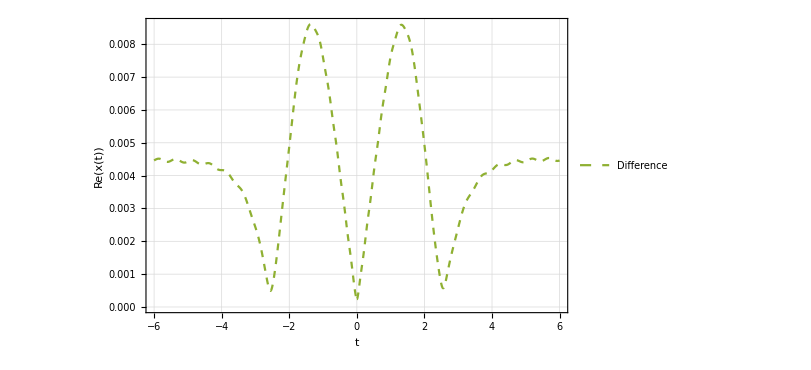

```mathematica
Plot[Evaluate[Re@Abs[{
xExact[ω,α,τ,T][t]-xAdbUpto[0][A,ϕ,ω,α,τ,T][t]
}/.icExactValues/.icAdbNorm[0][ω,α,τ,T]/.paramValues/.T->1
]],{t,-6,6},
PlotStyle->{ColorData[97,3],Dashed},ImageSize->600,PlotPoints->300,
BaseStyle->{FontFamily->"CMU Serif",FontSize->10},
AxesLabel->{ToExpression["t",TeXForm,HoldForm],ToExpression["\\mathrm{Re}\\left[x(t)\\right]",TeXForm,HoldForm]},
PlotLegends->Placed[LineLegend[{"Difference"},LegendFunction->(Framed[#,FrameMargins->0,FrameStyle->Gray,Background->White]&)],{Right,Bottom}],
GridLines->Automatic,Frame->True
]
```

### Adiabatic vs. numerical

#### Full adiabatic

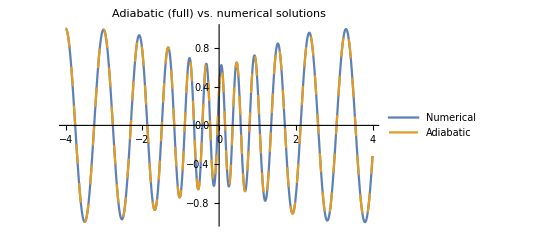

```mathematica
Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}/.paramValues/.T->1
]],relevantdomain,
PlotStyle->stylecompare,
PlotLegends->{"Numerical","Adiabatic"},
PlotLabel->"Adiabatic (full) vs. numerical solutions"]
```

### Numerical vs. semi-analytical

#### Full adiabatic

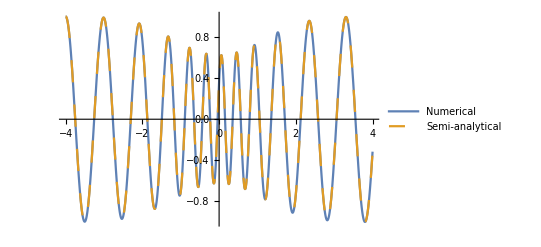

```mathematica
Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdbNum[A,ω,α,τ,T][t]
}/.paramValues/.T->1
]],relevantdomain,
PlotLegends->{"Numerical","Semi-analytical"},
PlotStyle->{SolidData,Dashing[0.04]}
]
```

### Adiabatic semi-analytical vs. analytical

#### Full adiabatic solution

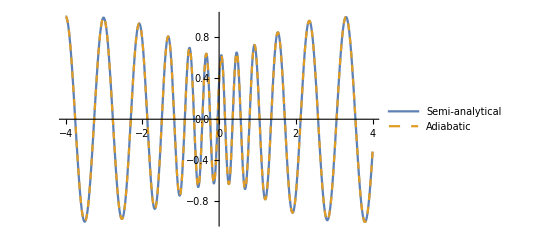

```mathematica
Plot[Evaluate[Re[{
xAdbNum[A,ω,α,τ,T][t],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}/.paramValues/.T->1
]],relevantdomain,
PlotLegends->{"Semi-analytical","Adiabatic"},
PlotStyle->{SolidData,Dashed}]
```

#### 0th-order adiabatic solution

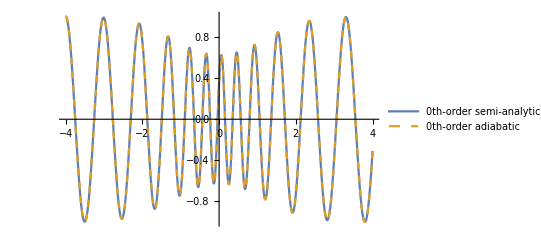

```mathematica
Plot[Evaluate[Re[{
xAdbNumUpto[0][A,ω,α,τ,T][t],
xAdbUpto[0][A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}/.paramValues/.T->1
]],relevantdomain,
PlotLegends->{"0th-order semi-analytical","0th-order adiabatic"},
PlotStyle->{SolidData,Dashed}]
```

#### 2nd-order adiabatic solution

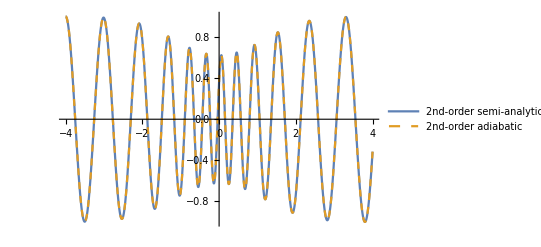

```mathematica
Plot[Evaluate[Re[{
xAdbNumUpto[2][A,ω,α,τ,T][t],
xAdbUpto[2][A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}/.paramValues/.T->1
]],relevantdomain,
PlotLegends->{"2nd-order semi-analytical","2nd-order adiabatic"},
PlotStyle->{SolidData,Dashed}]
```

## Parametric comparisons (manipulable)

### Numerical vs. exact

#### Manipulable plot

```mathematica
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xExact[ω,α,τ,T][t]/.icExactParam[A,ω,α,τ,T]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"Numerical","Exact"},
PlotStyle->stylecompare3
],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### Numerical vs. adiabatic

#### Manipulable plot

```mathematica
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"Numerical","Adiabatic"},
PlotStyle->stylecompare3
],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### Manipulable plot - Adiabatic regime

```mathematica
{
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T],
PoschlTeller[ω,α,τ][t]/ω
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->Placed[{"Numerical","Adiabatic","Ω(t)/ω"},{Right,Top}],
PlotStyle->stylecompare3],
Style["Initial conditions",12],{{A,1},0.1,10},(*{{ϕ,1.31947},0,2π},*)
Style["Parameters",12],{{ω,2π},0.1,30},{{α,18},0.1,30},{{τ,0.5},0.05,10},
Style["Adiabatic regime",12],{{T,1},0.1,20},
Style["Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
,
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T],
PoschlTeller[ω,α,τ][t]/ω
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->Placed[{"Numerical","Adiabatic","Ω(t)/ω"},{Right,Top}],
PlotStyle->stylecompare3],
Style["Initial conditions",12],{{A,1},0.1,10},(*{{ϕ,1.48283},0,2π},*)
Style["Parameters",12],{{ω,2π},0.1,30},{{α,18},0.1,30},{{τ,0.1},0.05,10},
Style["Adiabatic regime",12],{{T,1},0.1,20},
Style["Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
}
```

{,}

#### Manipulable plot - Sudden regime, two different ω ’s

```mathematica
{
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T],
PoschlTeller[ω,α,τ][t]/ω
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->Placed[{"Numerical","Adiabatic","Ω(t)/ω"},{Left,Top}],
PlotStyle->stylecompare3],
Style["Initial conditions",12],{{A,1},0.1,10},(*{{ϕ,0.82938},0,2π},*)
Style["Parameters",12],{{ω,2π},0.1,30},{{α,18},0.1,30},{{τ,0.06},0.05,10},
Style["Adiabatic regime",12],{{T,1},0.1,20},
Style["Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
,
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T],
PoschlTeller[ω,α,τ][t]/ω
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotRange->{-1.9,3.3},
PlotLegends->Placed[{"Numerical","Adiabatic","Ω(t)/ω"},{Left,Top}],
PlotStyle->stylecompare3
],
Style["Initial conditions",12],{{A,1},0.1,10},(*{{ϕ,0.82938},0,2π},*)
Style["Parameters",12],{{ω,4π},0.1,30},{{α,18},0.1,30},{{τ,0.06},0.05,10},
Style["Adiabatic regime",12],{{T,1},0.1,20},
Style["Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
}
```

{,}

### Adiabatic semi-analytical vs. analytical

#### Full adiabatic solution

```mathematica
Manipulate[Plot[Evaluate[Re[{
xAdbNum[A,ω,α,τ,T][t],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"Semi-analytical","Adiabatic"},
PlotStyle->{SolidData,Dashed}
],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### 0th-order adiabatic solution

```mathematica
Manipulate[Plot[Evaluate[Re[{
xAdbNumUpto[0][A,ω,α,τ,T][t],
xAdbUpto[0][A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"0th-order semi-analytical","0th-order adiabatic"},
PlotStyle->{SolidData,Dashed}],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

#### 2nd-order adiabatic solution

```mathematica
Manipulate[Plot[Evaluate[Re[{
xAdbNumUpto[2][A,ω,α,τ,T][t],
xAdbUpto[2][A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"2nd-order semi-analytical","2nd-order adiabatic"},
PlotStyle->{SolidData,Dashed}
],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

### Numerical vs. semi-analytical

↪︎ This emulates the exact vs. adiabatic comparison, with the advantage of being computed very fast so we can plot any parameters we like.
      However, the numerical error becomes too big for very small τ ’s, and the analytical adiabatic solutions are much better there.
      Hence, this is useful to test any range of the parameters ω and α, but not τ.
      Also, I think there is some mistake in the computation of the initial phase (probably only at second order).

#### Manipulable plot

```mathematica
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdbNum[A,ω,α,τ,T][t]
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->{"Numerical","Semi-analytical"},
PlotStyle->{SolidData,Dashing[0.04]}],
Style["
Initial conditions",12],{{A,1},0.1,10},Style["
Parameters",12],{{ω,2 π},0.1,30},{{α,15},0.1,30},{{τ,1},0.05,10},Style["
Adiabatic regime",12],{{T,1},0.1,20},Style["
Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

## Representative plot: WKB approximation vs. exact (numerical) solution

```mathematica
Manipulate[Plot[Evaluate[Re[{
xNum[t][A,ω,α,τ,T],
xAdb[A,ϕ,ω,α,τ,T][t]/.icAdbNorm[0][ω,α,τ,T],
PoschlTeller[ω,α,τ][t]/ω
}]],{t,Center-WindowSize/2,Center+WindowSize/2},
PlotLegends->Placed[{"Numerical^*","Adiabatic","Ω(t)/ω"},{Right,Top}],
PlotStyle->stylecompare3,
ImageSize->600],
Style["Initial conditions",12],{{A,1},0.1,10},(*{{ϕ,1.31947},0,2π},*)
Style["Parameters",12],{{ω,2π},0.1,30},{{α,18},0.1,30},{{τ,0.5},0.05,10},
Style["Adiabatic regime",12],{{T,1},0.1,20},
Style["Manipulate graph",12],{{WindowSize,2Abs[ti],"⟷ "},0.01,tmax/3},{{Center,0," ←  →"},tmin+WindowSize+0.01,tmax-WindowSize-0.01}]
```

ReplaceAll::reps: {icAdbNorm[0][2 π,18,0.5,1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {icAdbNorm[0.][6.28319,18.,0.5,1.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {icAdbNorm[0][2 π,18,0.5,1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {icAdbNorm[0.][6.28319,18.,0.5,1.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

* We compare the adiabatic WKB approximation with the numerical solution because the exact one, even though it admits a closed form result in terms of hypergeometric functions, is too slow to plot in Mathematica for manipulable parameters.